# Polygenic dynamics underlying the response of quantitative traits to directional selection

## Hannah Götsch and Reinhard Bürger

## 1. Efficient evaluation of the approximations for the phenotypic mean and variance

Below we collect definitions and routines to efficiently evaluate several of the quantities in Section 4 of the paper.

## 1.1. Efficient evaluation of the exponential integral

Because expressions of the form Exp[x] ExpIntegralE[1,x]] are not evaluated accurately (or not at all) if x > 80, we use the following approximation (Abramowitz and Stegun, 1964, Chap. 5.1) (note ExpIntegralE[1,x] = Gamma[0,x]):

```mathematica
expEInt1[x_]:=Exp[x]ExpIntegralE[1,x]
expEInt2[x_]:=1/x-1/x^2+2/x^3-6/x^4
expEInt[x_]:=If[x<50,expEInt1[x],expEInt2[x]]
```

## 1.2. Approximations for exponential distributed mutation effects

The most accurate approximations for the phenotypic mean and variance are given in Proposition 4.3 in the paper. However, those are not easy to evaluate efficiently for exponential distributed mutation effects. Therefore, we focus here on the simpler, but still accurate (apart from the very, very early phase), approximations given in Result 4.11. Result 4.11 is stated for the initial phase in the paper, but the approximations can also be used in the stationary phase (here even simpler approximations are valid; see Proposition 4.5).

From now on we assume θ  = 1 . Since the dependence on θ  is linear for the phenotypic mean and variance, the generalisation is straightforward.
Mutation effects are drawn from an exponential distribution with mean 1. Approximations for equal mutation effects and for mutation effects drawn from a truncated normal distribution can be evaluated analogously.

### 1.2.1. Some definitions and assumptions

First, we define the survival probability Psur and the quantity νnum  = Nn Psur:

```mathematica
Psur[s_]:=1+ProductLog[-Exp[s]/Exp[Exp[s]]]/Exp[s]
νnum[Nn_,s_,α_]:=Nn (1+ⅇ^(-s α) ProductLog[-ⅇ^(-ⅇ^(s α)+s α)])
```

We need to find out when νnum > 50. With the approx νnum ≈ 2 Nn s α, the critical α  = 25/(Nn s) .
In addition, we need to find when νnum Exp[-s α τ] > 50 . This needs to be done numerically:

```mathematica
froot[Nn_,s_,τ_]:=α/.FindRoot[α s τ== Log[Nn α s/25],{α,2}]
```

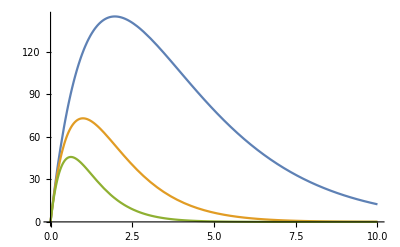

```mathematica
Plot[{Exp[-α s τ]νnum[Nn,s,α]/.{Nn->10^4,s->0.01,τ->50},Exp[-α s τ]νnum[Nn,s,α]/.{Nn->10^4,s->0.01,τ->100},Exp[-α s τ]νnum[Nn,s,α]/.{Nn->10^4,s->0.01,τ->160}},{α,0,10},PlotRange->All]
```

```mathematica
Simplify[Limit[Exp[-α s τ]νnum[Nn,s,α],α->Infinity,Assumptions->Nn>0&&s>0&&τ>0]]
```

0

Therefore, there are two or zero critical values  (or one in the exceptional case). For numerical purposes and an exponential distribution with mean 1, values α  in excess of 20 can be neglected.

```mathematica
nsolvefvals[Nn_,s_,τ_]:=nsolvefvals[Nn,s,τ]=α/.NSolve[α s τ== Log[Nn α s/25],α,Reals]
nsolvef[Nn_,s_,τ_]:=nsolvef[Nn,s,τ]=Which[Length[nsolvefvals[Nn,s,τ]]==2,nsolvefvals[Nn,s,τ],Length[nsolvefvals[Nn,s,τ]]==1,{nsolvefvals[Nn,s,τ][[1]],20},Length[nsolvefvals[Nn,s,τ]]==0,{21,22}]
```

```mathematica
{nsolvefvals[10^4,0.01,20],nsolvef[10^4,0.01,20]}
```

{{0.26353,22.4988},{0.26353,22.4988}}

```mathematica
{nsolvefvals[10^4,0.01,100],nsolvef[10^4,0.01,100]}
```

{{0.357403,2.15329},{0.357403,2.15329}}

```mathematica
{nsolvefvals[10^4,0.01,150],nsolvef[10^4,0.01,150]}
```

{α,{21,22}}

### 1.2.2. Computing the phenotypic mean Gbar(τ )

We use the approximation expEInt2[x] instead of the exact expEInt1[x] if x > 50, which is the case for α1 = nsolvefvals[Nn,s,τ][[1]] < α < α2 = nsolvefvals[Nn,s,τ][[2]] (provided they exist). 
Therefore, we compute gbarn1=∫_0^∞ ⅇ^-α P_sur[s α]ⅇ^ν E1[ν] ⅆα and gbarn2=∫_0^∞ ⅇ^-α P_sur[s α]ⅇ^(νⅇ^-sατ) E1[ν ⅇ^-sατ] ⅆα  as follows:

```mathematica
gbarn1[Nn_,s_]:=NIntegrate[Psur [s α] Exp[-α]expEInt1[νnum[Nn,s,α]],{α,0,25./(Nn s)}]+NIntegrate[Psur [s α] Exp[-α]expEInt2[νnum[Nn,s,α]],{α,25./(Nn s),Infinity}]
gbarn2[Nn_,s_,τ_]:=Which[nsolvef[Nn,s,τ][[1]]<20&&nsolvef[Nn,s,τ][[2]]<20,NIntegrate[Psur [s α] Exp[-α]expEInt1[Exp[-α s τ]νnum[Nn,s,α]],{α,0,nsolvef[Nn,s,τ][[1]]}]+NIntegrate[Psur [s α] Exp[-α]expEInt2[Exp[-α s τ]νnum[Nn,s,α]],{α,nsolvef[Nn,s,τ][[1]],nsolvef[Nn,s,τ][[2]]}]+NIntegrate[Psur [s α] Exp[-α]expEInt1[Exp[-α s τ]νnum[Nn,s,α]],{α,nsolvef[Nn,s,τ][[2]],20}],nsolvef[Nn,s,τ][[1]]<20&&nsolvef[Nn,s,τ][[2]]>20,NIntegrate[Psur [s α] Exp[-α]expEInt1[Exp[-α s τ]νnum[Nn,s,α]],{α,0,nsolvef[Nn,s,τ][[1]]}]+NIntegrate[Psur [s α] Exp[-α]expEInt2[Exp[-α s τ]νnum[Nn,s,α]],{α,nsolvef[Nn,s,τ][[1]],20}],nsolvef[Nn,s,τ][[1]]>20,NIntegrate[Psur [s α] Exp[-α]expEInt1[Exp[-α s τ]νnum[Nn,s,α]],{α,0,20}]]
```

The approximation for the phenotypic mean in the initial phase (Proposition 4.11) is then given by:

```mathematica
gbarnall[Nn_,s_,τ_]:=1/s(gbarn2[Nn,s,τ]-gbarn1[Nn,s])
```

This works quite well.
We can also compare this with the approximation for the very early phase (Proposition 4.13):

```mathematica
barGearly[Nn_,s_,τ_]:= τ/Nn(1+s τ+(s τ)^2 +(s τ)^3 )
```

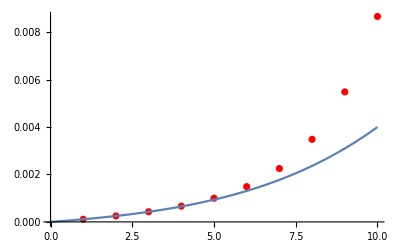

```mathematica
Show[ListPlot[Table[{τ,gbarnall[10^4,0.1,τ]},{τ,1,10}],PlotStyle->Red],Plot[barGearly[10^4,0.1,τ],{τ,0,10}]]
```

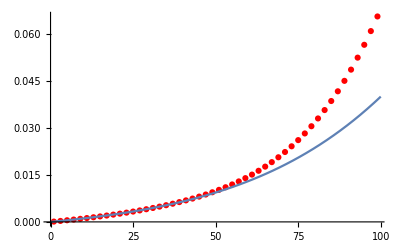

```mathematica
Show[ListPlot[Table[{τ,gbarnall[10^4,0.01,τ]},{τ,1,100,2}],PlotStyle->Red],Plot[barGearly[10^4,0.01,τ],{τ,0,100}]]
```

### 1.2.3. Computing the phenotypic variance VG(τ )

Analogously to Gbar, we define the approximation for the phenotypic variance in the initial phase (Proposition 4.11) as follows:

```mathematica
VGn1[Nn_,s_]:=NIntegrate[α Psur [s α] Exp[-α]νnum[Nn,s,α]expEInt1[νnum[Nn,s,α]],{α,0,25./(Nn s)}]+NIntegrate[α Psur [s α] Exp[-α]νnum[Nn,s,α]expEInt2[νnum[Nn,s,α]],{α,25./(Nn s),Infinity}];
VGn2[Nn_,s_,τ_]:=Which[nsolvef[Nn,s,τ][[1]]<20&&nsolvef[Nn,s,τ][[2]]<20,NIntegrate[α Psur [s α] Exp[-α]Exp[-α s τ]νnum[Nn,s,α]expEInt1[Exp[-α s τ]νnum[Nn,s,α]],{α,0,nsolvef[Nn,s,τ][[1]]}]+NIntegrate[α Psur [s α] Exp[-α]Exp[-α s τ]νnum[Nn,s,α]expEInt2[Exp[-α s τ]νnum[Nn,s,α]],{α,nsolvef[Nn,s,τ][[1]],nsolvef[Nn,s,τ][[2]]}]+NIntegrate[α Psur [s α] Exp[-α]Exp[-α s τ]νnum[Nn,s,α]expEInt1[Exp[-α s τ]νnum[Nn,s,α]],{α,nsolvef[Nn,s,τ][[2]],20}],nsolvef[Nn,s,τ][[1]]<20&&nsolvef[Nn,s,τ][[2]]>20,NIntegrate[α Psur [s α] Exp[-α]Exp[-α s τ]νnum[Nn,s,α]expEInt1[Exp[-α s τ]νnum[Nn,s,α]],{α,0,nsolvef[Nn,s,τ][[1]]}]+NIntegrate[α Psur [s α] Exp[-α]Exp[-α s τ]νnum[Nn,s,α]expEInt2[Exp[-α s τ]νnum[Nn,s,α]],{α,nsolvef[Nn,s,τ][[1]],20}],nsolvef[Nn,s,τ][[1]]>20,NIntegrate[α Psur [s α] Exp[-α]Exp[-α s τ]νnum[Nn,s,α]expEInt1[Exp[-α s τ]νnum[Nn,s,α]],{α,0,20}]];
VGnall[Nn_,s_,τ_]:=1/s(VGn1[Nn,s]-VGn2[Nn,s,τ])
```

We can also compare this with the approximation for the very early phase (Proposition 4.13):

```mathematica
VGearly[Nn_,s_,τ_]:= (2τ)/Nn(1+(3s τ)/2+2(s τ)^2 +(5(s τ)^3)/2 )
```

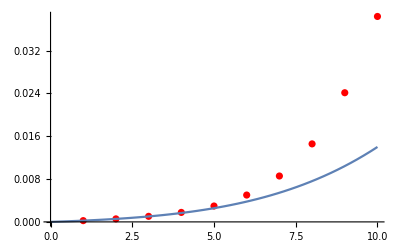

```mathematica
Show[ListPlot[Table[{τ,VGnall[10^4,0.1,τ]},{τ,0,10}],PlotStyle->Red],Plot[VGearly[10^4,0.1,τ],{τ,0,10}],PlotRange->All]
```

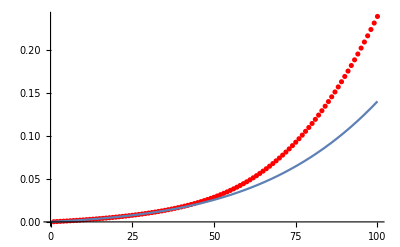

```mathematica
Show[ListPlot[Table[{τ,VGnall[10^4,0.01,τ]},{τ,0,100}],PlotStyle->Red],Plot[VGearly[10^4,0.01,τ],{τ,0,100}],PlotRange->All]
```

The following is the simple approximation for the stationary variance (Corollary 4.8):

```mathematica
VGinf[Nn_,s_]:=4(1-(5s)/2-1/(4Nn s))
```

Now, we compare all three approximations  (VGnall is the most accurate):

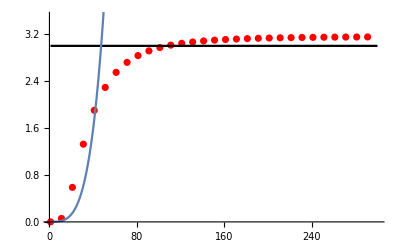

```mathematica
Show[ListPlot[Table[{τ,VGnall[10^4,0.1,τ]},{τ,1,300,10}],PlotStyle->Red],Plot[VGinf[10^4,0.1],{τ,1,300},PlotStyle->Black],Plot[VGearly[10^4,0.1,τ],{τ,1,50}],PlotRange->{0,3.5}]
```

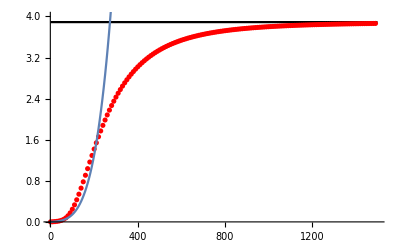

```mathematica
Show[ListPlot[Table[{τ,VGnall[10^4,0.01,τ]},{τ,1,1500,10}],PlotStyle->Red],Plot[VGinf[10^4,0.01],{τ,1,1500},PlotStyle->Black],Plot[VGearly[10^4,0.01,τ],{τ,1,300}],PlotRange->{0,4}]
```

## 2. Number of segregating sites and response of the mean

Here, we  compute (see also Section 5 and Appendix D of the paper)
	the branching process approximation, Stilde, for the expected number E[S] of segregating sites;
	the stationary value of E[S] using the diffusion approximation, SbarStat;
	the mean genotypic value Gbar on the basis of Result 4.11 in the paper for equal, GbarEqual, and for exponential distributed, GbarExp, mutation effects;
	the time Tbeta until Gbar reaches a specified value β;
	and Stilde(Tbeta). 
Moreover, we explore the dependence of the number of segregating sites and of the average time (after some mean phenotype is reached in the population) on the mutation effect. 
We assume equal mutation effects in 2.1. and 2.2., and exponential effects in 2.3.

## 2.1. Some definitions and values for equal mutation effects

Below, Ppol[s][τ ] is the probability that the mutant is present at time τ  :

```mathematica
Ppol[s_][0]:=1;
Ppol[s_][τ_]:=Ppol[s][τ]=1-Exp[-Exp[s]Ppol[s][τ-1]];
```

```mathematica
tfixHPh[Nn_,s_]:=(2(Log[2 Nn s]+EulerGamma-1/(2Nn s)))/s
tfixsmall[Nn_,s_]:=2Nn -(4 Nn^2 s)/27 (11-6 EulerGamma-6Log[3])
```

Here is our approximation for tfix (from Chapter 3 below):

```mathematica
tfixapp[Nn_,s_]:=Piecewise[{{tfixHPh[Nn,s],2Nn s>=3},{tfixsmall[Nn,s],2Nn s<3}}]
```

```mathematica
tildetau[τ_,α_,s_,Nn_]:=Min[τ,tfixapp[Nn,Exp[s α]-1]]
```

The neutral value of the number of segregating sites S :

```mathematica
Sneut[Θ_,Nn_]:=2Θ(Log[Nn]+EulerGamma)
```

Just for curiosity: neutral values of S:

```mathematica
Table[Transpose[Table[{{"Θ=",Θ},{"Nn=",Nn},{"S=",N[Sneut[Θ,Nn]]}},{Nn,{10^3,10^4,10^5}}]],{Θ,{5,0.5,0.05}}]//TableForm
```

Θ= | 5
Θ= | 5
Θ= | 5 | Nn= | 1000
Nn= | 10000
Nn= | 100000 | S= | 74.8497
S= | 97.8756
S= | 120.901
Θ= | 0.5
Θ= | 0.5
Θ= | 0.5 | Nn= | 1000
Nn= | 10000
Nn= | 100000 | S= | 7.48497
S= | 9.78756
S= | 12.0901
Θ= | 0.05
Θ= | 0.05
Θ= | 0.05 | Nn= | 1000
Nn= | 10000
Nn= | 100000 | S= | 0.748497
S= | 0.978756
S= | 1.20901

The stationary value of segregating sites S :

```mathematica
SbarStat[Θ_,α_,s_,Nn_]:=2Θ((1-s α)(Log[Nn]+Log[2Nn s α])+1+EulerGamma-(2EulerGamma+1/2)s α)
```

Stilde from the branching process approximation (equal effects!):

```mathematica
StildeEq[τ_,Θ_,α_,s_,Nn_]:=StildeEq[τ,Θ,α,s,Nn]=Θ Sum[Ppol[α s][j],{j,0,Round[tildetau[τ,α,s,Nn]]}]
```

We need the accurate approximation from Result 4.11 in the paper (see also Chapter 1 above) for Gbar.

We use the following asymptotic approximation for Exp[x]ExpIntegralE[1,x] if x is large:

```mathematica
expexpIntE[x_]:=If[x>=50,1/x-1/x^2,Exp[x] ExpIntegralE[1,x]]
```

```mathematica
GbarEqual[τ_,Θ_,α_,s_,Nn_]:=2Θ α (expexpIntE[2Nn s α Exp[-s α τ]]-expexpIntE[2Nn s α])
```

Note that Gbar is proportional to Θ and to α ! Otherwise, it depends only and s α and N (and τ, of course).

The number of generations until β  is reached:

```mathematica
Tbeta[Θ_,α_,s_,Nn_,β_]:=Tbeta[Θ,α,s,Nn,β]=τ/.FindRoot[GbarEqual[τ,Θ,α,s,Nn]==β,{τ,100/α}]
```

```mathematica
Tbeta[0.5,1,0.1,10^4,1]
```

84.3461

Now, we compute Stilde at the time Tbeta when β  is reached:

```mathematica
StildeBeta[Θ_,α_,s_,Nn_,β_]:={StildeEq[Tbeta[Θ,α,s,Nn,β],Θ,α,s,Nn],Tbeta[Θ,α,s,Nn,β]}
```

```mathematica
StildeBeta[0.05,1,0.1,10^4,1]
```

{1.60931,181.783}

```mathematica
StildeBeta[0.05,1,0.001,10^4,1]
```

{1.33477,13620.4}

The following correspond to the values given in Figure 5.2 in Section 5 of the paper:

```mathematica
StildeBeta[0.5,1,0.1,10^4,1]
```

{9.46584,84.3461}

```mathematica
StildeBeta[0.5,1,0.001,10^4,1]
```

{10.2001,3911.83}

```mathematica
StildeBeta[5,1,0.1,10^4,1]
```

{67.0221,53.9974}

```mathematica
StildeBeta[5,1,0.001,10^4,1]
```

{71.8723,1222.92}

## 2.2. Stilde(Tbeta) for equal mutation effects

For different combinations of parameters and as a function of α, the left plots show
	(Solid)		Stilde at the time Tbeta when β  is reached,
	(Dashed)		the stationary values, SbarStat, of S.
The right plots show on a logarithmic scale
	(Solid)		the time Tbeta when β  is reached,
	(Dashed)		the expected time to fixation (then the stationary value of S is (almost) attained).

Throughout: Different colors are for different population sizes (blue - 10^3, orange - 10^4, green - 10^5).

The figures below demonstrate that
	(i) the major determinant of Stilde(Tbeta) is θ, 
	(ii) the influence of Nn is approximately logarithmic, and 
	(iii) the effective strength of selection on individual loci (mediated by the average mutation affect α, where 0 < α  ≤ 1) changes Stilde(Tbeta) by at most a factor of two . 
They also show that there is an interaction effect of θ  and α . This gets stronger for larger Nn .

### Scaling options for Gbar

#### 2.2.1. In units of α (Choose β = k α ; k = 1,2)

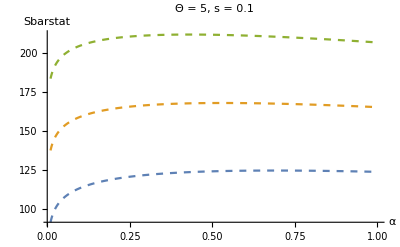

```mathematica
Plot[{SbarStat[5,α,0.1,10^3],SbarStat[5,α,0.1,10^4],SbarStat[5,α,0.1,10^5]},{α,0.01,1},AxesLabel->{α,"Sbarstat"},PlotLabel->"Θ = 5, s = 0.1",PlotStyle->Dashed,PlotRange->All]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

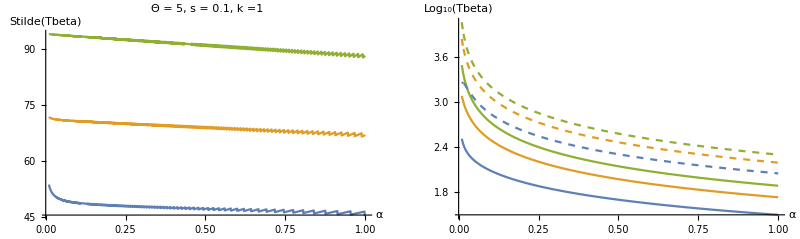

```mathematica
GraphicsGrid[{{Plot[{StildeBeta[5,α,0.1,10^3,α][[1]],StildeBeta[5,α,0.1,10^4,α][[1]],StildeBeta[5,α,0.1,10^5,α][[1]]},{α,0.01,1},AxesLabel->{α,"Stilde(Tbeta)"},PlotLabel->"Θ = 5, s = 0.1, k =1",PlotRange->All],
Show[Plot[{Log[10,Tbeta[5,α,0.1,10^3,α]],Log[10,Tbeta[5,α,0.1,10^4,α]],Log[10,Tbeta[5,α,0.1,10^5,α]]},{α,0.01,1},AxesLabel->{α,"Log_10(Tbeta)"},PlotRange->All],Plot[{Log[10,tfixapp[10^3,Exp[0.1α]-1]],Log[10,tfixapp[10^4,Exp[0.1α]-1]],Log[10,tfixapp[10^5,Exp[0.1α]-1]]},{α,0.01,1},AxesLabel->{α,"Log_10(tfix)"},PlotStyle->Dashed,PlotRange->All]]}},ImageSize->800]
```

The above shows that for Θ = 5 Gbar reaches β much earlier than tfix.

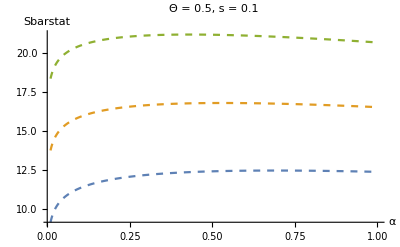

```mathematica
Plot[{SbarStat[0.5,α,0.1,10^3],SbarStat[0.5,α,0.1,10^4],SbarStat[0.5,α,0.1,10^5]},{α,0.01,1},AxesLabel->{α,"Sbarstat"},PlotLabel->"Θ = 0.5, s = 0.1",PlotStyle->Dashed,PlotRange->All]
```

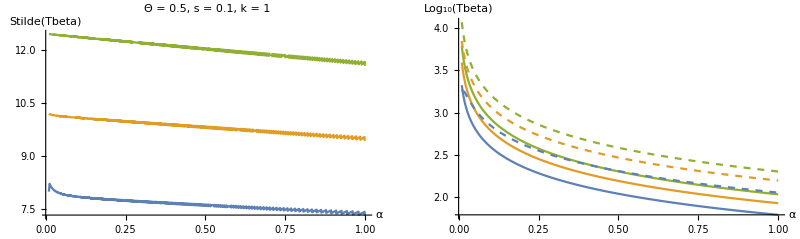

```mathematica
GraphicsGrid[{{Plot[{StildeBeta[0.5,α,0.1,10^3,α][[1]],StildeBeta[0.5,α,0.1,10^4,α][[1]],StildeBeta[0.5,α,0.1,10^5,α][[1]]},{α,0.01,1},AxesLabel->{α,"Stilde(Tbeta)"},PlotLabel->"Θ = 0.5, s = 0.1, k = 1", PlotRange->All],
Show[Plot[{Log[10,Tbeta[0.5,α,0.1,10^3,α]],Log[10,Tbeta[0.5,α,0.1,10^4,α]],Log[10,Tbeta[0.5,α,0.1,10^5,α]]},{α,0.01,1},AxesLabel->{α,"Log_10(Tbeta)"},PlotRange->All],
Plot[{Log[10,tfixapp[10^3,Exp[0.1α]-1]],Log[10,tfixapp[10^4,Exp[0.1α]-1]],Log[10,tfixapp[10^5,Exp[0.1α]-1]]},{α,0.01,1},AxesLabel->{α,"Log_10(tfix)"},PlotStyle->Dashed,PlotRange->All]]}},ImageSize->800]
```

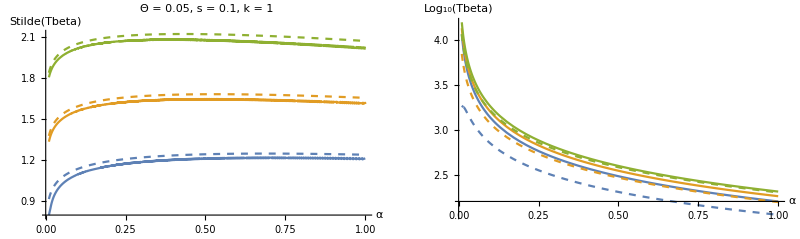

```mathematica
GraphicsGrid[{{Show[Plot[{StildeBeta[0.05,α,0.1,10^3,α][[1]],StildeBeta[0.05,α,0.1,10^4,α][[1]],StildeBeta[0.05,α,0.1,10^5,α][[1]]},{α,0.01,1},AxesLabel->{α,"Stilde(Tbeta)"},PlotLabel->"Θ = 0.05, s = 0.1, k = 1",PlotRange->All],
Plot[{SbarStat[0.05,α,0.1,10^3],SbarStat[0.05,α,0.1,10^4],SbarStat[0.05,α,0.1,10^5]},{α,0.01,1},AxesLabel->{α,"Sbarstat"},PlotLabel->"Θ = 0.05, s = 0.1",PlotStyle->Dashed,PlotRange->All]],Show[Plot[{Log[10,Tbeta[0.05,α,0.1,10^3,α]],Log[10,Tbeta[0.05,α,0.1,10^4,α]],Log[10,Tbeta[0.05,α,0.1,10^5,α]]},{α,0.01,1},AxesLabel->{α,"Log_10(Tbeta)"},PlotRange->All],
Plot[{Log[10,tfixapp[10^3,Exp[0.1α]-1]],Log[10,tfixapp[10^4,Exp[0.1α]-1]],Log[10,tfixapp[10^5,Exp[0.1α]-1]]},{α,0.01,1},AxesLabel->{α,"Log_10(tfix)"},PlotStyle->Dashed,PlotRange->All]]}},ImageSize->800]
```

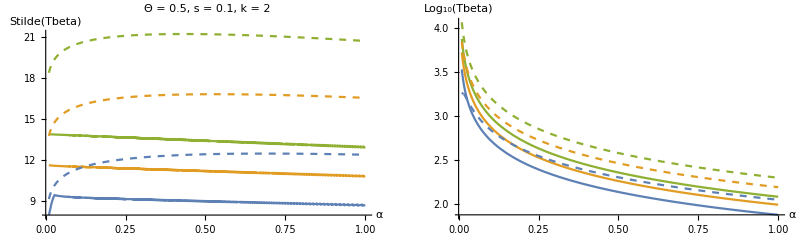

```mathematica
GraphicsGrid[{{Show[Plot[{StildeBeta[0.5,α,0.1,10^3,2α][[1]],StildeBeta[0.5,α,0.1,10^4,2α][[1]],StildeBeta[0.5,α,0.1,10^5,2α][[1]]},{α,0.01,1},AxesLabel->{α,"Stilde(Tbeta)"},PlotLabel->"Θ = 0.5, s = 0.1, k = 2",PlotRange->All],
Plot[{SbarStat[0.5,α,0.1,10^3],SbarStat[0.5,α,0.1,10^4],SbarStat[0.5,α,0.1,10^5]},{α,0.01,1},AxesLabel->{α,"Sbarstat"},PlotLabel->"Θ = 0.5, s = 0.1",PlotStyle->Dashed,PlotRange->All]],Show[Plot[{Log[10,Tbeta[0.5,α,0.1,10^3,2α]],Log[10,Tbeta[0.5,α,0.1,10^4,2α]],Log[10,Tbeta[0.5,α,0.1,10^5,2α]]},{α,0.01,1},AxesLabel->{α,"Log_10(Tbeta)"},PlotRange->All],
Plot[{Log[10,tfixapp[10^3,Exp[0.1α]-1]],Log[10,tfixapp[10^4,Exp[0.1α]-1]],Log[10,tfixapp[10^5,Exp[0.1α]-1]]},{α,0.01,1},AxesLabel->{α,"Log_10(tfix)"},PlotStyle->Dashed,PlotRange->All]]}},ImageSize->800]
```

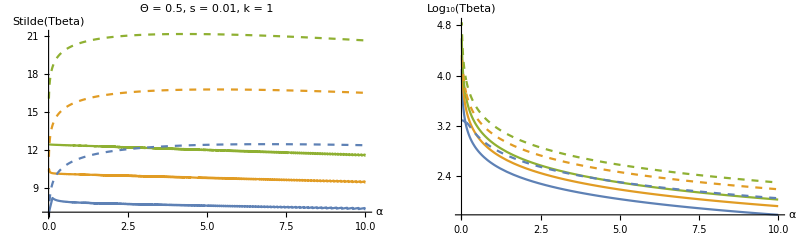

```mathematica
GraphicsGrid[{{Show[Plot[{StildeBeta[0.5,α,0.01,10^3,α][[1]],StildeBeta[0.5,α,0.01,10^4,α][[1]],StildeBeta[0.5,α,0.01,10^5,α][[1]]},{α,0.01,10},AxesLabel->{α,"Stilde(Tbeta)"},PlotLabel->"Θ = 0.5, s = 0.01, k = 1",PlotRange->All],
Plot[{SbarStat[0.5,α,0.01,10^3],SbarStat[0.5,α,0.01,10^4],SbarStat[0.5,α,0.01,10^5]},{α,0.01,10},AxesLabel->{α,"Sbarstat"},PlotLabel->"Θ = 0.5, s = 0.01",PlotStyle->Dashed,PlotRange->All]],Show[Plot[{Log[10,Tbeta[0.5,α,0.01,10^3,α]],Log[10,Tbeta[0.5,α,0.01,10^4,α]],Log[10,Tbeta[0.5,α,0.01,10^5,α]]},{α,0.01,10},AxesLabel->{α,"Log_10(Tbeta)"},PlotRange->All],
Plot[{Log[10,tfixapp[10^3,Exp[0.01α]-1]],Log[10,tfixapp[10^4,Exp[0.01α]-1]],Log[10,tfixapp[10^5,Exp[0.01α]-1]]},{α,0.01,10},AxesLabel->{α,"Log_10(tfix)"},PlotStyle->Dashed,PlotRange->All]]}},ImageSize->800]
```

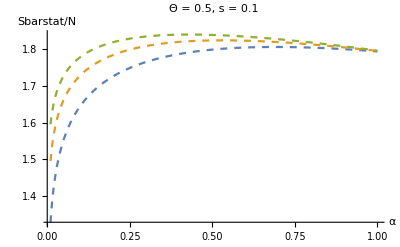

```mathematica
GraphicsGrid[{{
Plot[{SbarStat[0.5,α,0.1,10^3]/Log[10^3],SbarStat[0.5,α,0.1,10^4]/Log[10^4],SbarStat[0.5,α,0.1,10^5]/Log[10^5]},{α,0.01,1},AxesLabel->{α,"Sbarstat/N"},PlotLabel->"Θ = 0.5, s = 0.1",PlotStyle->Dashed,PlotRange->All]
}},ImageSize->400]
```

#### 2.2.2. In arbitrary units (e.g., in environmental or phenotypic standard deviations)

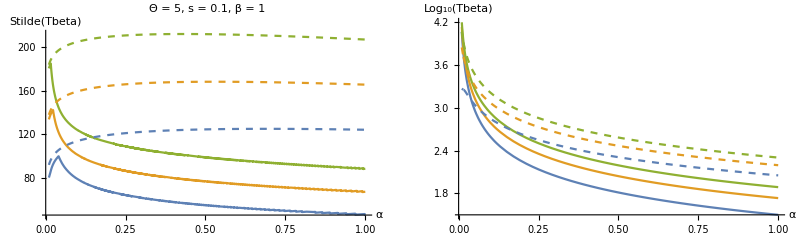

```mathematica
GraphicsGrid[{{Show[Plot[{StildeBeta[5,α,0.1,10^3,1][[1]],StildeBeta[5,α,0.1,10^4,1][[1]],StildeBeta[5,α,0.1,10^5,1][[1]]},{α,0.01,1},AxesLabel->{α,"Stilde(Tbeta)"},PlotLabel->"Θ = 5, s = 0.1, β = 1", PlotRange->All],Plot[{SbarStat[5,α,0.1,10^3],SbarStat[5,α,0.1,10^4],SbarStat[5,α,0.1,10^5]},{α,0.01,1},AxesLabel->{α,"Sbarstat"},PlotStyle->Dashed,PlotRange->All]],Show[Plot[{Log[10,Tbeta[5,α,0.1,10^3,1]],Log[10,Tbeta[5,α,0.1,10^4,1]],Log[10,Tbeta[5,α,0.1,10^5,1]]},{α,0.01,1},AxesLabel->{α,"Log_10(Tbeta)"},PlotRange->All],Plot[{Log[10,tfixapp[10^3,Exp[0.1α]-1]],Log[10,tfixapp[10^4,Exp[0.1α]-1]],Log[10,tfixapp[10^5,Exp[0.1α]-1]]},{α,0.01,1},AxesLabel->{α,"Log_10(tfix)"},PlotStyle->Dashed,PlotRange->All]]}},ImageSize->800]
```

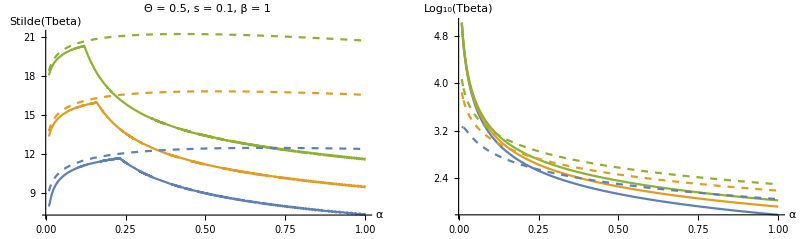

```mathematica
GraphicsGrid[{{Show[Plot[{StildeBeta[0.5,α,0.1,10^3,1][[1]],StildeBeta[0.5,α,0.1,10^4,1][[1]],StildeBeta[0.5,α,0.1,10^5,1][[1]]},{α,0.01,1},AxesLabel->{α,"Stilde(Tbeta)"},PlotLabel->"Θ = 0.5, s = 0.1, β = 1", PlotRange->All],Plot[{SbarStat[0.5,α,0.1,10^3],SbarStat[0.5,α,0.1,10^4],SbarStat[0.5,α,0.1,10^5]},{α,0.01,1},AxesLabel->{α,"Sbarstat"},PlotStyle->Dashed,PlotRange->All]],Show[Plot[{Log[10,Tbeta[0.5,α,0.1,10^3,1]],Log[10,Tbeta[0.5,α,0.1,10^4,1]],Log[10,Tbeta[0.5,α,0.1,10^5,1]]},{α,0.01,1},AxesLabel->{α,"Log_10(Tbeta)"},PlotRange->All],Plot[{Log[10,tfixapp[10^3,Exp[0.1α]-1]],Log[10,tfixapp[10^4,Exp[0.1α]-1]],Log[10,tfixapp[10^5,Exp[0.1α]-1]]},{α,0.01,1},AxesLabel->{α,"Log_10(tfix)"},PlotStyle->Dashed,PlotRange->All]]}},ImageSize->800]
```

Above, the kinks in S occur when Tbeta exceeds tfix, hence the stationary value of S is reached.

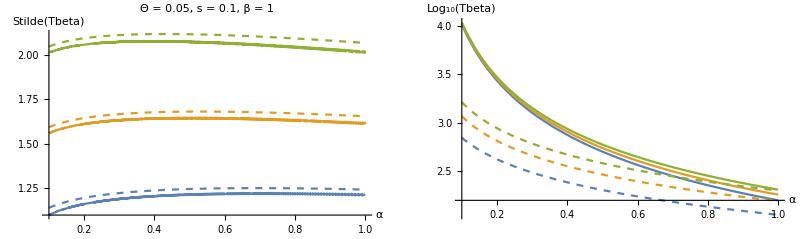

```mathematica
GraphicsGrid[{{Show[Plot[{StildeBeta[0.05,α,0.1,10^3,1][[1]],StildeBeta[0.05,α,0.1,10^4,1][[1]],StildeBeta[0.05,α,0.1,10^5,1][[1]]},{α,0.1,1},AxesLabel->{α,"Stilde(Tbeta)"},PlotLabel->"Θ = 0.05, s = 0.1, β = 1", PlotRange->All],Plot[{SbarStat[0.05,α,0.1,10^3],SbarStat[0.05,α,0.1,10^4],SbarStat[0.05,α,0.1,10^5]},{α,0.1,1},AxesLabel->{α,"Sbarstat"},PlotStyle->Dashed,PlotRange->All]],Show[Plot[{Log[10,Tbeta[0.05,α,0.1,10^3,1]],Log[10,Tbeta[0.05,α,0.1,10^4,1]],Log[10,Tbeta[0.05,α,0.1,10^5,1]]},{α,0.1,1},AxesLabel->{α,"Log_10(Tbeta)"},PlotRange->All],Plot[{Log[10,tfixapp[10^3,Exp[0.1α]-1]],Log[10,tfixapp[10^4,Exp[0.1α]-1]],Log[10,tfixapp[10^5,Exp[0.1α]-1]]},{α,0.1,1},AxesLabel->{α,"Log_10(tfix)"},PlotStyle->Dashed,PlotRange->All]]}},ImageSize->800]
```

In the above graphs,Tbeta always exceeds tfix.

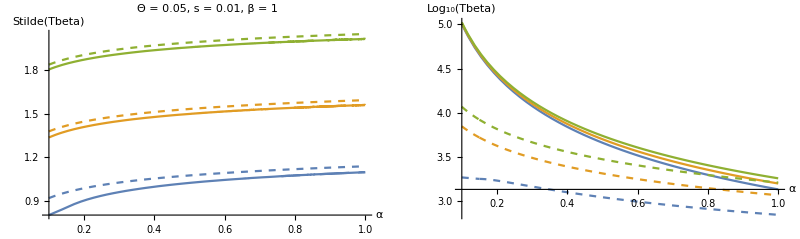

```mathematica
GraphicsGrid[{{Show[Plot[{StildeBeta[0.05,α,0.01,10^3,1][[1]],StildeBeta[0.05,α,0.01,10^4,1][[1]],StildeBeta[0.05,α,0.01,10^5,1][[1]]},{α,0.1,1},AxesLabel->{α,"Stilde(Tbeta)"},PlotLabel->"Θ = 0.05, s = 0.01, β = 1", PlotRange->All],Plot[{SbarStat[0.05,α,0.01,10^3],SbarStat[0.05,α,0.01,10^4],SbarStat[0.05,α,0.01,10^5]},{α,0.1,1},AxesLabel->{α,"Sbarstat"},PlotStyle->Dashed,PlotRange->All]],Show[Plot[{Log[10,Tbeta[0.05,α,0.01,10^3,1]],Log[10,Tbeta[0.05,α,0.01,10^4,1]],Log[10,Tbeta[0.05,α,0.01,10^5,1]]},{α,0.1,1},AxesLabel->{α,"Log_10(Tbeta)"},PlotRange->All],Plot[{Log[10,tfixapp[10^3,Exp[0.01α]-1]],Log[10,tfixapp[10^4,Exp[0.01α]-1]],Log[10,tfixapp[10^5,Exp[0.01α]-1]]},{α,0.1,1},AxesLabel->{α,"Log_10(tfix)"},PlotStyle->Dashed,PlotRange->All]]}},ImageSize->800]
```

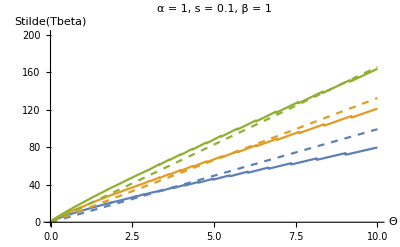

```mathematica
Show[{Plot[{StildeBeta[Θ,1,0.1,10^3,1][[1]],StildeBeta[Θ,1,0.1,10^4,1][[1]],StildeBeta[Θ,1,0.1,10^5,1][[1]]},{Θ,0.001,10},AxesLabel->{Θ,"Stilde(Tbeta)"},PlotLabel->"α = 1, s = 0.1, β = 1", PlotRange->All],Plot[{SbarStat[Θ,1,0.1,10^3]/2.5,SbarStat[Θ,1,0.1,10^4]/2.5,SbarStat[Θ,1,0.1,10^5]/2.5},{Θ,0.001,10},AxesLabel->{Θ,"Sbarstat"},PlotStyle->Dashed,PlotRange->All]},PlotRange->{0,200}]
```

StildeBeta increases slightly slower than linear in Θ.

## 2.3. Stilde(Tbeta) for exponential distributed mutation effects

We define Gbar according to Result 4.11 in the paper (see also Chapter 1 above).

```mathematica
GbarExp[τ_,Θ_,abar_,s_,Nn_]:=GbarExp[τ,Θ,abar,s,Nn]=1/abar NIntegrate[Exp[-α/abar]GbarEqual[τ,Θ,α,s,Nn],{α,0.001abar,7abar}];
GbarExp[0,Θ_,abar_,s_,Nn_]:=0
```

Taking the integral above over α  between 0.001 abar and 7 abar is a good approximation:

```mathematica
Integrate[1/abar Exp[-α/abar],{α,0.001abar,7abar},Assumptions->abar>0]//N
```

0.998089

For efficient plotting, we need tables of GbarExp values (to be able to use ListLinePlot instead of Plot).

```mathematica
GbarExpTab[tend_,Θ_,abar_,s_,Nn_]:=Table[{τ,GbarExp[τ,Θ,abar,s,Nn]},{τ,0,tend}]
```

The following takes about 32 seconds (for 100 values):

```mathematica
Timing[GbarExpTab[100,0.5,1,0.1,10^4]]
```

{32.4844,{{0,0},{1,0.0000549359},{2,0.000123018},{3,0.000209198},{4,0.00032092},{5,0.000469629},{6,0.00067329},{7,0.000960631},{8,0.00137819},{9,0.00200205},{10,0.00295552},{11,0.00443377},{12,0.00673081},{13,0.010257},{14,0.0155312},{15,0.0231424},{16,0.0336915},{17,0.0477368},{18,0.0657587},{19,0.0881455},{20,0.115195},{21,0.147122},{22,0.184071},{23,0.226127},{24,0.273324},{25,0.325654},{26,0.383076},{27,0.445519},{28,0.51289},{29,0.58508},{30,0.661963},{31,0.743405},{32,0.829264},{33,0.919391},{34,1.01364},{35,1.11185},{36,1.21388},{37,1.31958},{38,1.42879},{39,1.54138},{40,1.65721},{41,1.77613},{42,1.89802},{43,2.02274},{44,2.15018},{45,2.28021},{46,2.41272},{47,2.54761},{48,2.68476},{49,2.82408},{50,2.96547},{51,3.10884},{52,3.2541},{53,3.40118},{54,3.54998},{55,3.70044},{56,3.85248},{57,4.00604},{58,4.16104},{59,4.31743},{60,4.47515},{61,4.63414},{62,4.79435},{63,4.95572},{64,5.1182},{65,5.28176},{66,5.44635},{67,5.61191},{68,5.77843},{69,5.94584},{70,6.11413},{71,6.28324},{72,6.45316},{73,6.62385},{74,6.79528},{75,6.96741},{76,7.14023},{77,7.3137},{78,7.48781},{79,7.66252},{80,7.83781},{81,8.01367},{82,8.19006},{83,8.36698},{84,8.5444},{85,8.7223},{86,8.90067},{87,9.07949},{88,9.25874},{89,9.4384},{90,9.61847},{91,9.79893},{92,9.97977},{93,10.161},{94,10.3425},{95,10.5244},{96,10.7066},{97,10.8891},{98,11.072},{99,11.2551},{100,11.4385}}}

Here, Gbar is displayed as a function of time for exponential distributed  (red) and equal (blue) mutation effects:

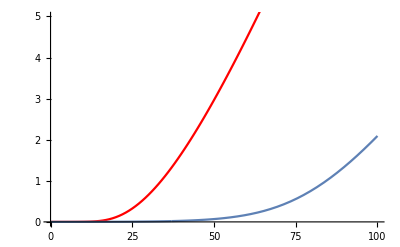

```mathematica
Show[ListLinePlot[GbarExpTab[100,0.5,1,0.1,10^4],PlotStyle->Red],Plot[GbarEqual[τ,0.5,1,0.1,10^4],{τ,0,100}],PlotRange->{0,5}]
```

Their ratio shows that the response for an exponential distribution is initially much faster but slows down later on:

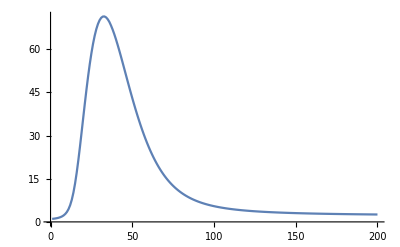

```mathematica
ListLinePlot[Table[GbarExp[τ,0.5,1,0.1,10^4]/GbarEqual[τ,0.5,1,0.1,10^4],{τ,1,200}]]
```

```mathematica
GbarExp[200,0.5,1,0.1,10^4]/GbarEqual[200,0.5,1,0.1,10^4]
```

2.57363

Now, we compute the time (TbetaExp) until GbarExp reaches β:

```mathematica
TbetaExp[Θ_,abar_,s_,Nn_,β_]:=TbetaExp[Θ,abar,s,Nn,β]=(t=1;While[GbarExp[t,Θ,abar,s,Nn]<β,t++];taugamma=t)
```

The following takes about 2 minutes (time until β reached for exponential distributed (TbetaExp) and equal (Tbeta) mutation effects):

```mathematica
TbetaExp[0.5,1,0.01,10^4,1]
```

271

```mathematica
Tbeta[0.5,1,0.01,10^4,1]
```

613.993

```mathematica
TbetaExp[0.5,1,0.1,10^4,1]
```

34

```mathematica
Tbeta[0.5,1,0.1,10^4,1]
```

84.3461

Not surprisingly, with an exponential distribution the response is considerably faster.

Here, the time until β is reached is displayed as a function of the (mean) mutation effect for exponential distributed (red; TbetaExp) and equal (blue; Tbeta) mutation effects:

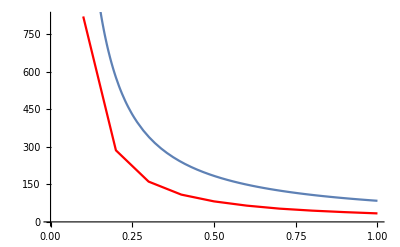

```mathematica
Show[{ListLinePlot[Table[{abar,TbetaExp[0.5,abar,0.1,10^4,1]},{abar,0.1,1,0.1}],PlotStyle->Red],Plot[Tbeta[0.5,a,0.1,10^4,1],{a,0.1,1}]}]
```

Their ratio:

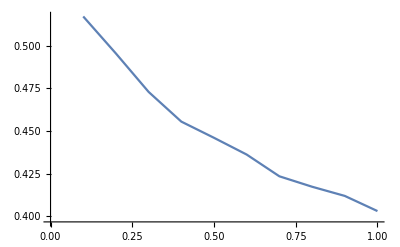

```mathematica
ListLinePlot[Table[{abar,TbetaExp[0.5,abar,0.1,10^4,1]/Tbeta[0.5,abar,0.1,10^4,1]},{abar,0.1,1,0.1}]]
```

Here, TbetaExp is displayed as a function of abar for Θ  = 0.5 (red) and 5 (blue); s = 0.1, N = 10^4:

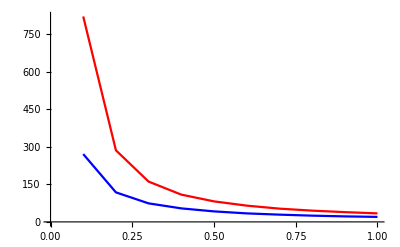

```mathematica
Show[{ListLinePlot[Table[{abar,TbetaExp[0.5,abar,0.1,10^4,1]},{abar,0.1,1,0.1}],PlotStyle->Red],ListLinePlot[Table[{abar,TbetaExp[5,abar,0.1,10^4,1]},{abar,0.1,1,0.1}],PlotStyle->Blue]}]
```

Their ratio:

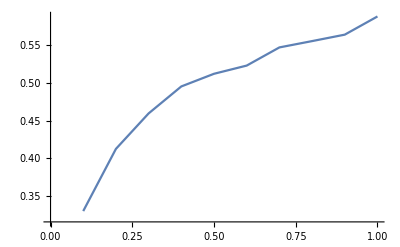

```mathematica
ListLinePlot[Table[{abar,TbetaExp[5,abar,0.1,10^4,1]/TbetaExp[0.5,abar,0.1,10^4,1]},{abar,0.1,1,0.1}]]
```

With this values the corresponding S can be computed.

```mathematica
StildefEq[τ_,Θ_,abar_,s_,Nn_]:=StildefEq[τ,Θ,abar,s,Nn]=Θ/abar Sum[NIntegrate[Exp[-α/abar]Ppol[α s][j],{α,0.001abar,7abar}],{j,0,τ}]
```

Here, the corresponding S - values are shown (Θ  = 0.5 (red), Θ  = 5 (blue)):

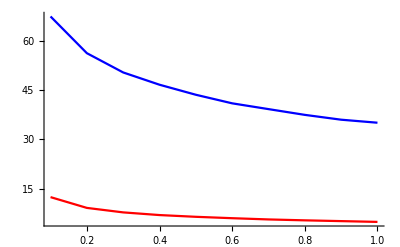

```mathematica
Show[ListLinePlot[Table[{abar,StildefEq[TbetaExp[0.5,abar,0.1,10^4,1],0.5,abar,0.1,10^4]},{abar,0.1,1,0.1}],PlotStyle->Red],ListLinePlot[Table[{abar,StildefEq[TbetaExp[5,abar,0.1,10^4,1],5,abar,0.1,10^4]},{abar,0.1,1,0.1}],PlotStyle->Blue],PlotRange->All]
```

Now we show Stilde for exponential (solid) and equal (dashed) effects on a Log10 scale:

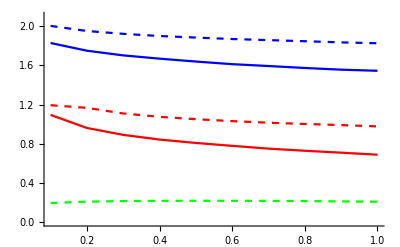

```mathematica
Show[ListLinePlot[Table[{abar,Log[10,StildefEq[TbetaExp[0.5,abar,0.1,10^4,1],0.5,abar,0.1,10^4]]},{abar,0.1,1,0.1}],PlotStyle->Red],ListLinePlot[Table[{abar,Log[10,StildefEq[TbetaExp[5,abar,0.1,10^4,1],5,abar,0.1,10^4]]},{abar,0.1,1,0.1}],PlotStyle->Blue],ListLinePlot[Table[{abar,Log[10,StildeEq[Tbeta[0.5,abar,0.1,10^4,1],0.5,abar,0.1,10^4]]},{abar,0.1,1,0.1}],PlotStyle->Directive[Red,Dashed]],ListLinePlot[Table[{abar,Log[10,StildeEq[Tbeta[5,abar,0.1,10^4,1],5,abar,0.1,10^4]]},{abar,0.1,1,0.1}],PlotStyle->Directive[Blue,Dashed]],ListLinePlot[Table[{abar,Log[10,StildeEq[Tbeta[0.05,abar,0.1,10^4,1],0.05,abar,0.1,10^4]]},{abar,0.1,1,0.1}],PlotStyle->Directive[Green,Dashed]],PlotRange->{0,2.1},AxesOrigin->{0,0}]
```

#### Data for the above plots

```mathematica
Table[{abar,StildeEq[Tbeta[0.05,abar,0.1,10^4,1],0.05,abar,0.1,10^4]},{abar,0.1,1,0.1}]
```

{{0.1,1.55894},{0.2,1.61038},{0.3,1.63235},{0.4,1.64205},{0.5,1.64424},{0.6,1.64258},{0.7,1.63973},{0.8,1.63127},{0.9,1.61967},{1.,1.60931}}

```mathematica
Table[{abar,Log[10,StildeEq[Tbeta[0.05,abar,0.1,10^4,1],0.05,abar,0.1,10^4]]},{abar,0.1,1,0.1}]
```

{{0.1,0.19283},{0.2,0.206928},{0.3,0.212814},{0.4,0.215386},{0.5,0.215966},{0.6,0.215526},{0.7,0.214771},{0.8,0.212525},{0.9,0.209426},{1.,0.20664}}

```mathematica
Table[{abar,StildefEq[TbetaExp[0.05,abar,0.1,10^4,1],0.05,abar,0.1,10^4],TbetaExp[0.05,abar,0.1,10^4,1]},{abar,0.1,1,0.1}]
```

{{0.1,5.80144,5475},{0.2,3.20218,1467},{0.3,2.3208,698},{0.4,1.87066,419},{0.5,1.59331,285},{0.6,1.40568,210},{0.7,1.26703,163},{0.8,1.15698,131},{0.9,1.07398,109},{1.,1.00804,93}}

```mathematica
Table[{abar,StildefEq[TbetaExp[0.5,abar,0.1,10^4,1],0.5,abar,0.1,10^4],TbetaExp[0.5,abar,0.1,10^4,1]},{abar,0.1,1,0.1}]
```

{{0.1,12.4051,821},{0.2,9.12282,286},{0.3,7.75488,161},{0.4,6.94043,109},{0.5,6.40989,82},{0.6,5.98725,65},{0.7,5.6094,53},{0.8,5.33474,45},{0.9,5.09906,39},{1.,4.86092,34}}

```mathematica
Table[{abar,StildefEq[TbetaExp[5,abar,0.1,10^4,1],5,abar,0.1,10^4],TbetaExp[5,abar,0.1,10^4,1]},{abar,0.1,1,0.1}]
```

{{0.1,67.411,271},{0.2,56.2302,118},{0.3,50.3622,74},{0.4,46.6251,54},{0.5,43.5719,42},{0.6,40.9608,34},{0.7,39.2002,29},{0.8,37.4485,25},{0.9,35.9774,22},{1.,35.0556,20}}

```mathematica
Table[{abar,StildeEq[Tbeta[0.05,abar,0.1,10^4,1],0.05,abar,0.1,10^4],Tbeta[0.05,abar,0.1,10^4,1]},{abar,0.1,1,0.1}]
```

{{0.1,1.55894,10588.1},{0.2,1.61038,2828.56},{0.3,1.63235,1343.64},{0.4,1.64205,806.577},{0.5,1.64424,549.719},{0.6,1.64258,405.58},{0.7,1.63973,315.827},{0.8,1.63127,255.695},{0.9,1.61967,213.159},{1.,1.60931,181.783}}

```mathematica
Table[{abar,StildeEq[Tbeta[0.5,abar,0.1,10^4,1],0.5,abar,0.1,10^4],Tbeta[0.5,abar,0.1,10^4,1]},{abar,0.1,1,0.1}]
```

{{0.1,15.5894,1588.02},{0.2,14.6482,577.402},{0.3,12.8415,340.493},{0.4,11.8549,239.317},{0.5,11.2142,183.865},{0.6,10.7175,149.023},{0.7,10.3208,125.162},{0.8,10.0243,107.823},{0.9,9.76512,94.6652},{1.,9.46584,84.3461}}

```mathematica
Table[{abar,StildeEq[Tbeta[5,abar,0.1,10^4,1],5,abar,0.1,10^4],Tbeta[5,abar,0.1,10^4,1]},{abar,0.1,1,0.1}]
```

{{0.1,100.835,613.993},{0.2,89.4116,287.227},{0.3,83.617,186.866},{0.4,79.44,138.36},{0.5,76.6196,109.81},{0.6,74.0385,91.0121},{0.7,72.1396,77.7026},{0.8,70.2728,67.7858},{0.9,68.3923,60.1118},{1.,67.0221,53.9974}}

## 3. Expected time to fixation or loss of a favorable mutant: Diffusion approximations

Below we collect definitions and routines to efficiently evaluate several of the quantities in Appendix B of the paper. Moreover, information beyond Appendix B is provided.

First, we assume a given selective coefficient s, then effects are drawn from an (exponential) distribution.
We assume a haploid population of size Nn and an advantageous mutant occurring initially as a single copy. The starting point are the diffusion approximation results for the sojourn time densities in Ewens (1979, 2004).

## 3.1. Sojourn time densities

For a haploid population of size Nn (and adapting Ewens’ parameterization, who considers diploids , Ewens 1979, Chapter 5, p. 138), we have α  → 2 Nn s, where s is the selective advantage of the mutant, i.e., fitnesses are 1 and 1+s. A single advantageous mutant starts at relative frequency p=1/Nn.

The following is the fixation probability of the mutant (Ewens 1979, p. 147; eq. (5.46))

```mathematica
pfix[p_,α_]:=(1-Exp[-α p])/(1-Exp[-α])
```

The sojourn time density conditional on fixation of the favorable mutant is the following (Ewens 1979, pp. 150 - 151; eqs (5.51), (5.52)! There is a typo in eq. (5.51), which is corrected below):

```mathematica
tast1[x_,p_,α_]:=(2 (Exp[α x]-1)^2Exp[-α x](1-Exp[-α(1-p)]))/(α x(1-x)(1-Exp[-α])(Exp[α p]-1));
tast2[x_,p_,α_]:=(2 (Exp[α(1-x)]-1)(Exp[α x]-1))/(α x(1-x)(Exp[α]-1));
tast[x_,p_,α_]:=If[0≤x≤p,tast1[x,p,α],tast2[x,p,α]]
```

Here, p is the initial frequency of the mutant, and 0 ≤ x ≤ 1. Note that (Ewens 1979, p. 121, eq (4.26)) 
	∫_x1^x2 tast(x,p,α)ⅆx is the mean time in the diffusion process 	
	that the random variable spends in the interval (x1,x2) before absorption.
	This time is on the diffusion scale. To obtain the original time in the Markov process, tast and taast need to be multiplied by Nn.

Here is the sojourn time density conditional on loss of the favorable mutant:

```mathematica
taast1[x_,p_,α_]:=(2 (Exp[α x]-1)(Exp[α (1-x)]-1))/(α x(1-x)(Exp[α]-1));
taast2[x_,p_,α_]:=(2 Exp[-α(1-x)](Exp[α (1-x)]-1)^2(1-Exp[-α p]))/(α x(1-x)(1-Exp[-α])(Exp[α (1-p)]-1));
taast[x_,p_,α_]:=If[0≤x≤p,taast1[x,p,α],taast2[x,p,α]]
```

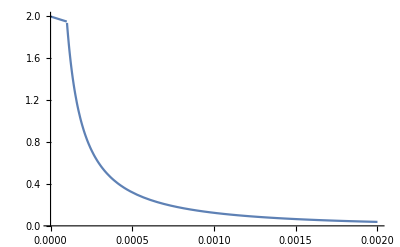

```mathematica
Plot[taast[x,10^(-4),500],{x,0,0.002},PlotRange->All]
```

```mathematica
N[{ Exp[-α(1-x)],(Exp[α (1-x)]-1)^2,(1-Exp[-α p]),α x(1-x),(1-Exp[-α]),(Exp[α (1-p)]-1)}]/.{α->50,p->0.0001,x->0.5}
```

{1.38879×10^-11,5.18471×10^21,0.00498752,12.5,1.,5.15885×10^21}

```mathematica
N[{ Exp[-α(1-x)],(Exp[α (1-x)]-1)^2,(1-Exp[-α p]),α x(1-x),(1-Exp[-α]),(Exp[α (1-p)]-1)}]/.{α->50,p->0.0001,x->0.0001}
```

{1.93842×10^-22,2.66137×10^43,0.00498752,0.0049995,1.,5.15885×10^21}

```mathematica
taast[0.9,10^(-4),500]
```

8.41731×10^-199

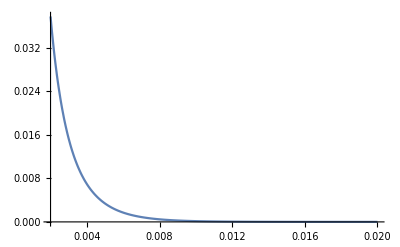

```mathematica
Plot[taast[x,10^(-4),500],{x,0.002,0.02},PlotRange->All]
```

## 3.2. Expected times to fixation or loss: Numeric and analytic integrals

### 3.2.1 Numerical integration and explicit (analytical) integrals

Numerical integration assuming a single mutant (p = 1/Nn) and α = 2 Nn s (and time in generations)

```mathematica
tfix1NInt[Nn_,s_]:=Nn NIntegrate[tast1[x,1/Nn,2Nn s],{x,0,1/Nn}];
tfix2NInt[Nn_,s_]:=Nn NIntegrate[tast2[x,1/Nn,2Nn s],{x,1/Nn,1}];
tfixNInt[Nn_,s_]:=tfix1NInt[Nn,s]+tfix2NInt[Nn,s];
tloss1NInt[Nn_,s_]:=Nn NIntegrate[taast1[x,1/Nn,2Nn s],{x,0,1/Nn}];
tloss2NInt[Nn_,s_]:=Nn NIntegrate[taast2[x,1/Nn,2Nn s],{x,1/Nn,1}];
tlossNInt[Nn_,s_]:=tloss1NInt[Nn,s]+tloss2NInt[Nn,s];
```

```mathematica
{tfix1NInt[1000,0.01],tfix2NInt[1000,0.01],tfixNInt[1000,0.01]}
```

{0.99071,702.039,703.03}

```mathematica
{tloss1NInt[1000,0.01],tloss2NInt[1000,0.01],tlossNInt[1000,0.01]}
```

{1.99104,6.88162,8.87266}

```mathematica
Simplify[Integrate[tast1[x,1/Nn,2Nn s],{x,0,1/Nn}],Assumptions->{Nn>1,s>0}]
```

((ⅇ^(2 s)-ⅇ^(2 Nn s)) (2 EulerGamma-ExpIntegralEi[-2 s]-ExpIntegralEi[2 s]+ⅇ^(2 Nn s) ExpIntegralEi[-2 (-1+Nn) s]+ⅇ^(-2 Nn s) ExpIntegralEi[2 (-1+Nn) s]-ⅇ^(2 Nn s) ExpIntegralEi[-2 Nn s]-ⅇ^(-2 Nn s) ExpIntegralEi[2 Nn s]-2 Log[(-1+Nn)/Nn]-2 Log[Nn]+1/2 Log[16 Nn^4 s^4]))/((-1+ⅇ^(2 s)) (-1+ⅇ^(2 Nn s)) Nn s)

```mathematica
Simplify[Integrate[tast2[x,1/Nn,2Nn s],{x,1/Nn,1}],Assumptions->{Nn>1,s>0}]
```

1/(2 (-1+ⅇ^(2 Nn s)) Nn s)(2 EulerGamma+2 ⅇ^(2 Nn s) EulerGamma+2 ⅇ^(2 Nn s) ExpIntegralEi[-2 s]+2 ExpIntegralEi[2 s]-2 ⅇ^(2 Nn s) ExpIntegralEi[-2 (-1+Nn) s]-2 ExpIntegralEi[2 (-1+Nn) s]-2 ⅇ^(2 Nn s) ExpIntegralEi[-2 Nn s]-2 ExpIntegralEi[2 Nn s]+2 Log[(-1+Nn)/Nn]+2 ⅇ^(2 Nn s) Log[(-1+Nn)/Nn]+2 Log[Nn]+2 ⅇ^(2 Nn s) Log[Nn]-ⅇ^(2 Nn s) Log[-1/(2 Nn s)]+ⅇ^(2 Nn s) Log[-2 Nn s]+Log[4 Nn^2 s^2])

These expressions can be slightly simplified.

```mathematica
tfix1ex[Nn_,s_]:=(ⅇ^(2 s)-ⅇ^(2 Nn s))/((-1+ⅇ^(2 s)) (-1+ⅇ^(2 Nn s))s) (2 EulerGamma-ExpIntegralEi[-2 s]-ExpIntegralEi[2 s]+ⅇ^(2 Nn s) ExpIntegralEi[-2 (-1+Nn) s]-ⅇ^(2 Nn s) ExpIntegralEi[-2 Nn s]+ⅇ^(-2 Nn s) ExpIntegralEi[2 (-1+Nn) s]-ⅇ^(-2 Nn s) ExpIntegralEi[2 Nn s]-2 Log[(-1+Nn)/Nn]-2 Log[Nn]+2 Log[2 Nn s]);
tfix2ex[Nn_,s_]:=1/((1-ⅇ^(2Nn s))s)(ExpIntegralEi[2Nn s]+ExpIntegralEi[2(Nn-1) s]-ExpIntegralEi[2s]-(EulerGamma+Log[Nn-1]+Log[2Nn s])+ⅇ^(2Nn s) (-ExpIntegralEi[-2s]+ExpIntegralEi[-2Nn s]+ExpIntegralEi[-2(Nn-1) s]-(EulerGamma+Log[Nn-1]+Log[2Nn s])));
tfixex[Nn_,s_]:=tfix1ex[Nn,s]+tfix2ex[Nn,s];
```

tfix1ex is always less than 1.

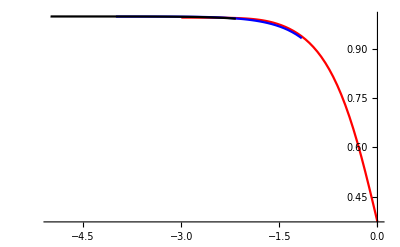

```mathematica
Show[{Plot[tfix1ex[100,10^s],{s,-3,0},PlotStyle->Red],Plot[tfix1ex[10^3,10^s],{s,-4,-1},PlotStyle->Blue],Plot[tfix1ex[10^4,10^s],{s,-5,-2},PlotStyle->Black]},PlotRange->All]
```

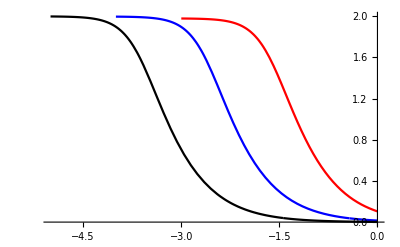

```mathematica
Show[{Plot[tfix2ex[100,10^s]/100,{s,-3,0},PlotStyle->Red],Plot[tfix2ex[10^3,10^s]/10^3,{s,-4,0},PlotStyle->Blue],Plot[tfix2ex[10^4,10^s]/10^4,{s,-5,0},PlotStyle->Black]},PlotRange->All]
```

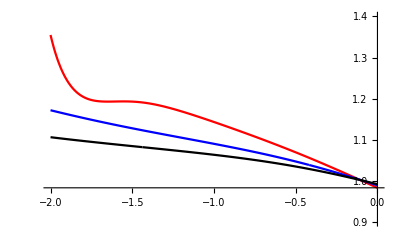

```mathematica
Show[{Plot[tfix2ex[100,10^s]/(2 Log[2 100 10^s]/10^s),{s,-2,0},PlotStyle->Red],Plot[tfix2ex[10^3,10^s]/(2 Log[2 10^3 10^s]/10^s),{s,-2,0},PlotStyle->Blue],Plot[tfix2ex[10^4,10^s]/(2 Log[2 10^4 10^s]/10^s),{s,-2,0},PlotStyle->Black]},PlotRange->{0.9,1.4}]
```

```mathematica
Simplify[Integrate[taast1[x,1/Nn,2Nn s],{x,0,1/Nn}],Assumptions->{Nn>1,s>0}]
```

1/(2 (-1+ⅇ^(2 Nn s)) Nn s)(2 EulerGamma+2 ⅇ^(2 Nn s) EulerGamma-2 ⅇ^(2 Nn s) ExpIntegralEi[-2 s]-2 ExpIntegralEi[2 s]+2 ⅇ^(2 Nn s) ExpIntegralEi[-2 (-1+Nn) s]+2 ExpIntegralEi[2 (-1+Nn) s]-2 ⅇ^(2 Nn s) ExpIntegralEi[-2 Nn s]-2 ExpIntegralEi[2 Nn s]-2 Log[(-1+Nn)/Nn]-2 ⅇ^(2 Nn s) Log[(-1+Nn)/Nn]-2 Log[Nn]-2 ⅇ^(2 Nn s) Log[Nn]-ⅇ^(2 Nn s) Log[-1/(2 Nn s)]+ⅇ^(2 Nn s) Log[-2 Nn s]+Log[4 Nn^2 s^2])

```mathematica
Simplify[Integrate[taast2[x,1/Nn,2Nn s],{x,1/Nn,1}],Assumptions->{Nn>1,s>0}]
```

-((ⅇ^(-2 s) (-1+ⅇ^(2 s)) (2 ⅇ^(4 Nn s) ExpIntegralEi[-2 s]+2 ExpIntegralEi[2 s]-2 ⅇ^(4 Nn s) ExpIntegralEi[-2 Nn s]-2 ExpIntegralEi[2 Nn s]-2 ⅇ^(2 Nn s) (ExpIntegralEi[-2 (-1+Nn) s]+ExpIntegralEi[2 (-1+Nn) s]-2 Log[-1+Nn])+ⅇ^(2 Nn s) (4 EulerGamma+Log[16 Nn^4 s^4])))/(2 (-1+ⅇ^(2 (-1+Nn) s)) (-1+ⅇ^(2 Nn s)) Nn s))

This expressions can be slightly simplified.

```mathematica
tloss1ex[Nn_,s_]:=-1/((ⅇ^(2 Nn s)-1) s)(ⅇ^(2 Nn s) ExpIntegralEi[-2 s]+ExpIntegralEi[2 s]-ⅇ^(2 Nn s) ExpIntegralEi[-2 (-1+Nn) s]-ExpIntegralEi[2 (-1+Nn) s]+ⅇ^(2 Nn s) ExpIntegralEi[-2 Nn s]+ExpIntegralEi[2 Nn s]-(1+ⅇ^(2 Nn s)) (EulerGamma+Log[2 Nn s]-Log[Nn-1]));
tloss2ex[Nn_,s_]:=(-1+ⅇ^(2 s))/((ⅇ^(2 s)-ⅇ^(2 Nn s)) (-1+ⅇ^(2 Nn s)) s) (ⅇ^(4 Nn s) ExpIntegralEi[-2 s]-ⅇ^(4 Nn s) ExpIntegralEi[-2 Nn s]+2 ⅇ^(2 Nn s) (EulerGamma+Log[-1+Nn]+Log[2 Nn s])-ⅇ^(2 Nn s) ExpIntegralEi[-2 (-1+Nn) s]-ⅇ^(2 Nn s) ExpIntegralEi[2 (-1+Nn) s]-ExpIntegralEi[2 Nn s]+ExpIntegralEi[2 s]);
tlossex[Nn_,s_]:=tloss1ex[Nn,s]+tloss2ex[Nn,s];
```

### 3.2.2 Approximations and asymptotics for tfix if Ns > 1

#### Derivation

Using the asymptotic approximation ExpIntegralEi[x] = Exp[x]/(x-1), which is very accurate if |x|>3, we obtain for tfix2ex (with x = 2 Nn s and Nn~(Nn-1) = x/(2s)):

```mathematica
Simplify[ 1/((1-ⅇ^x)s)(ⅇ^x 1/(x-1)+ⅇ^x 1/(x-1)-ExpIntegralEi[2s]-(EulerGamma+Log[x/(2s)]+Log[x])+ⅇ^x (-ExpIntegralEi[-2s]+ExpIntegralEi[-x]+ExpIntegralEi[-x]-(EulerGamma+Log[x/(2s)]+Log[x])))]
```

```mathematica
-1/(s-ⅇ^x s)(EulerGamma-(2 ⅇ^x)/(-1+x)+ExpIntegralEi[2 s]+Log[x]+Log[x/(2 s)]+ⅇ^x (EulerGamma+ExpIntegralEi[-2 s]-2 ExpIntegralEi[-x]+Log[x]+Log[x/(2 s)]))
```

-(EulerGamma-(2 ⅇ^x)/(-1+x)+ExpIntegralEi[2 s]+Log[x]+Log[x/(2 s)]+ⅇ^x (EulerGamma+ExpIntegralEi[-2 s]-2 ExpIntegralEi[-x]+Log[x]+Log[x/(2 s)]))/(s-ⅇ^x s)

```mathematica
Simplify[Limit[%/Log[x],x->Infinity,Assumptions->s>0]]
```

2/s

Therefore, asymptotically for large Nn s,  tfix2ex[Nn, s] ~ 2 Log[2 Nn s]/s.

As an approximation for tfix we use the (haploid version of the) Hermisson - Pennings approximation, which is very accurate if 2 Nn s > 3.

```mathematica
tfixHPh[Nn_,s_]:=(2(Log[2 Nn s]+EulerGamma-1/(2Nn s)))/s
```

For small s, it becomes negative . We compute the value, where it assumes its maximum :

```mathematica
Simplify[D[tfixHPh[Nn,s],s]]
```

(2-2 (-1+EulerGamma) Nn s-2 Nn s Log[2 Nn s])/(Nn s^3)

```mathematica
Simplify[Solve[2-2 (-1+EulerGamma) x-2 x Log[2 x]==0,x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1/ProductLog[2 ⅇ^(-1+EulerGamma)]}}

```mathematica
N[%]
```

{{x→1.49179}}

Therefore, the maximum is very close to Ns = 3/2.
For smaller values of s, we derive a linear approximation by using that tfix[Nn,0]=2Nn.

```mathematica
Simplify[(2Nn-tfixHPh[Nn,3/(2Nn)])/(3/(2Nn))]
```

-4/27 Nn^2 (-11+6 EulerGamma+Log[729])

We will use tfixsmall if Nn s < 3/2:

```mathematica
tfixsmall[Nn_,s_]:=2Nn -(4 Nn^2 s)/27 (11-6 EulerGamma-6Log[3])
```

```mathematica
Simplify[tfixsmall[Nn,3/(2Nn)]-tfixHPh[Nn,3/(2Nn)]]
```

0

Here is our approximation for tfix:

```mathematica
tfixapp[Nn_,s_]:=Piecewise[{{tfixHPh[Nn,s],2Nn s>=3},{tfixsmall[Nn,s],2Nn s<3}}]
```

#### Plots

```mathematica
linestyle1={Directive[AbsoluteThickness[2],Orange],Directive[AbsoluteThickness[2],Red],Directive[AbsoluteThickness[2],Red,Dashed],Directive[AbsoluteThickness[2],Black],Directive[AbsoluteThickness[2],RGBColor[0,0.1,1]]};legend1=LineLegend[linestyle1,{"t_fix^(small)", "t_fix^(HP)", "t_fix^(HP)", "t_fix^(exact)", "(t̄)_fix"},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->13],LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),LegendMargins->0];
```

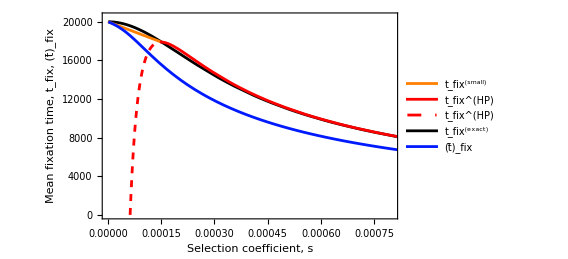

```mathematica
Nnn=10^4;plottfix1a=Plot[tfixsmall[Nnn,Exp[s]-1],{s,0,3/(2Nnn)},PlotRange->{0,2Nnn},PlotStyle->linestyle1[[1]],AxesOrigin->{0,0}];
plottfix1b=Plot[tfixHPh[Nnn,(Exp[s]-1)],{s,3/(2Nnn),0.01},PlotStyle->linestyle1[[{2}]],PlotRange->{0,2Nnn},Frame->{{True,False},{True,False}},FrameLabel->{Style["Selection coefficient, s",FontFamily->"Helvetica",FontSize->13,Black],Style["Mean fixation times, t_fix, (t̄)_fix",FontFamily->"Helvetica",FontSize->13,Black]},
LabelStyle->13,FrameTicksStyle->Directive[Black,13],ImageSize->400];
plottfix1c=Plot[tfixHPh[Nnn,(Exp[s]-1)],{s,0.00001,3/(2Nnn)},PlotStyle->linestyle1[[{3}]],PlotRange->{0,2Nnn}];
plottfix1d=Plot[tfixex[Nnn,(Exp[s]-1) ],{s,0.000001,0.01},PlotStyle->linestyle1[[{4}]],PlotRange->{0,2Nnn},Frame->{{True,False},{True,False}},FrameLabel->{Style["Selection coefficient, s",FontFamily->"Helvetica",FontSize->13,Black],Style["Mean fixation time, t_fix, (t̄)_fix",FontFamily->"Helvetica",FontSize->13,Black]},
LabelStyle->13,FrameTicksStyle->Directive[Black,13],ImageSize->420];plotbartfix1=Plot[bartfixnum[10^4,s],{s,10^(-6),0.001},PlotStyle->linestyle1[[5]]];
Legended[Show[{plottfix1d,plottfix1a,plottfix1b,plottfix1c,plotbartfix1},PlotRange->{{0,0.0008},{0,20500}}],Placed[legend1,{0.27,0.35}]]
```

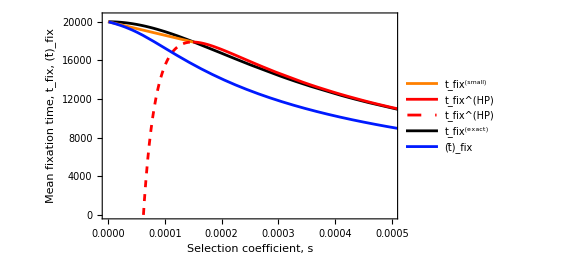

```mathematica
Legended[Show[{plottfix1d,plottfix1a,plottfix1b,plottfix1c,plotbartfix1},PlotRange->{{0,0.0005},{0,20500}}],Placed[legend1,{0.32,0.35}]]
```

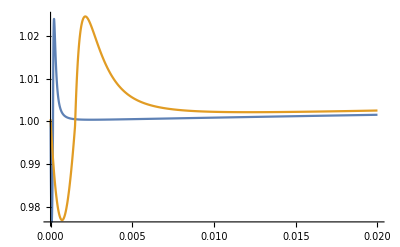

```mathematica
Plot[{tfixapp[10^4,s]/tfixNInt[10^4,s],tfixapp[10^3,s]/tfixNInt[10^3,s]},{s,0,0.02},PlotRange->All]
```

### 3.2.3 Approximations and asymptotics for tloss

#### Time spent in 0 < x < 1/(Nn) , tloss1ex (time scale in generations)

Start simplifications :

```mathematica
tloss1ex[Nn,s]
```

-1/((-1+ⅇ^(2 Nn s)) s)(ⅇ^(2 Nn s) ExpIntegralEi[-2 s]+ExpIntegralEi[2 s]-ⅇ^(2 Nn s) ExpIntegralEi[-2 (-1+Nn) s]-ExpIntegralEi[2 (-1+Nn) s]+ⅇ^(2 Nn s) ExpIntegralEi[-2 Nn s]+ExpIntegralEi[2 Nn s]-(1+ⅇ^(2 Nn s)) (EulerGamma-Log[-1+Nn]+Log[2 Nn s]))

```mathematica
N[-{ⅇ^(2 Nn s) ExpIntegralEi[-2 s],ExpIntegralEi[2 s],-ⅇ^(2 Nn s) ExpIntegralEi[-2 (-1+Nn) s],-ExpIntegralEi[2 (-1+Nn) s],ⅇ^(2 Nn s) ExpIntegralEi[-2 Nn s],ExpIntegralEi[2 Nn s],-(1+ⅇ^(2 Nn s)) (EulerGamma+Log[2 Nn s]-Log[Nn-1])}/((ⅇ^(2 Nn s)-1) s)/.{s->0.01,Nn->10^3}]
```

{335.471,6.83212×10^-7,-1.00438×10^-8,5.18072,9.83553×10^-9,-5.27978,-333.381}

```mathematica
N[-{ⅇ^(2 Nn s) ExpIntegralEi[-2 s],ExpIntegralEi[2 s],-ⅇ^(2 Nn s) ExpIntegralEi[-2 (-1+Nn) s],-ExpIntegralEi[2 (-1+Nn) s],ⅇ^(2 Nn s) ExpIntegralEi[-2 Nn s],ExpIntegralEi[2 Nn s],-(1+ⅇ^(2 Nn s)) (EulerGamma+Log[2 Nn s]-Log[Nn-1])}/((ⅇ^(2 Nn s)-1) s)/.{s->0.01,Nn->10^4}]
```

{335.471,4.58721×10^-85,-7.02502×10^-88,0.492624,6.88523×10^-88,-0.502525,-333.471}

Thus, numerics shows that we can neglect terms 2, 3, and 5.

To proceed analytically, we again use the asymptotic approximation ExpIntegralEi[x] = Exp[x]/(x-1) (|x|>3).

These three terms are of order Exp[-2 Nn s].

```mathematica
tloss1exapp1[Nn_,s_]:=-1/((-1+ⅇ^(2 Nn s)) s)(ⅇ^(2 Nn s) ExpIntegralEi[-2 s]-ExpIntegralEi[2 (-1+Nn) s]+ExpIntegralEi[2 Nn s]-(1+ⅇ^(2 Nn s)) (EulerGamma-Log[-1+Nn]+Log[2 Nn s]))
```

```mathematica
{tloss1ex[10^3,0.01],tloss1exapp1[10^3,0.01]}
```

{1.99104,1.99104}

Next we use Exp[2 Nn s] >> 1 and Nn >> 1.

```mathematica
Simplify[-1/((ⅇ^(2 Nn s)) s)(ⅇ^(2 Nn s) ExpIntegralEi[-2 s]-ExpIntegralEi[2 (Nn) s]+ExpIntegralEi[2 Nn s]-(ⅇ^(2 Nn s)) (EulerGamma-Log[Nn]+Log[2 Nn s]))]
```

(EulerGamma-ExpIntegralEi[-2 s]-Log[Nn]+Log[2 Nn s])/s

```mathematica
FullSimplify[-Log[Nn]+Log[2 Nn s]-Log[2s],Assumptions->{Nn>1,s>0}]
```

0

```mathematica
FullSimplify[-ExpIntegralEi[-2 s]+Log[2s],Assumptions->s>0]
```

-ExpIntegralEi[-2 s]+Log[2 s]

```mathematica
FullSimplify[Series[(EulerGamma-ExpIntegralEi[-2 s]+Log[2s])/s,{s,0,3}],Assumptions->s>0]
```

2-s+(4 s^2)/9+O[s]^3

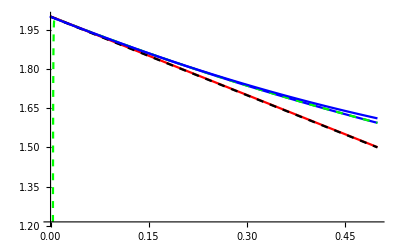

```mathematica
Plot[{tloss1ex[10^3,s],tloss1exapp1[10^3,s],tloss1hs[s,10^3],tloss1app[10^3,s],2-s+(4 s^2)/9},{s,0,0.5},PlotStyle->{Blue,Directive[Green,Dashed],Red,Directive[Black,Dashed]}]
```

We will use the following simple approximation:

```mathematica
tloss1app[Nn_,s_]:=2-s
```

#### Time spent in 1/(Nn) < x < 1 , tloss2ex (time scale in generations)

```mathematica
tloss2ex[Nn,s]
```

((-1+ⅇ^(2 s)) (ⅇ^(4 Nn s) ExpIntegralEi[-2 s]+ExpIntegralEi[2 s]-ⅇ^(2 Nn s) ExpIntegralEi[-2 (-1+Nn) s]-ⅇ^(2 Nn s) ExpIntegralEi[2 (-1+Nn) s]-ⅇ^(4 Nn s) ExpIntegralEi[-2 Nn s]-ExpIntegralEi[2 Nn s]+2 ⅇ^(2 Nn s) (EulerGamma+Log[-1+Nn]+Log[2 Nn s])))/((ⅇ^(2 s)-ⅇ^(2 Nn s)) (-1+ⅇ^(2 Nn s)) s)

Only the first two terms of the sum in parenthesis are of order Exp[4 Nn s] (again, using the above asymptotics for ExpIntegralEi).

```mathematica
N[(-1+ⅇ^(2 s))/((ⅇ^(2 s)-ⅇ^(2 Nn s)) (-1+ⅇ^(2 Nn s)) s) {ⅇ^(4 Nn s) ExpIntegralEi[-2 s],-ⅇ^(2 Nn s) ExpIntegralEi[2 (-1+Nn) s],-ⅇ^(4 Nn s) ExpIntegralEi[-2 Nn s],-ExpIntegralEi[2 Nn s],+2 ⅇ^(2 Nn s) (EulerGamma+Log[-1+Nn]+Log[2 Nn s]),+ExpIntegralEi[2 s],-ⅇ^(2 Nn s) ExpIntegralEi[-2 (-1+Nn) s]}/.{s->0.1,Nn->30}]
```

{2.72195,0.406156,-0.000801641,0.00117623,-0.0633097,0.0000112406,-2.50071×10^-6}

```mathematica
N[(-1+ⅇ^(2 s))/((ⅇ^(2 s)-ⅇ^(2 Nn s)) (-1+ⅇ^(2 Nn s)) s) {ⅇ^(4 Nn s) ExpIntegralEi[-2 s],-ⅇ^(2 Nn s) ExpIntegralEi[2 (-1+Nn) s],-ⅇ^(4 Nn s) ExpIntegralEi[-2 Nn s],-ExpIntegralEi[2 Nn s],+2 ⅇ^(2 Nn s) (EulerGamma+Log[-1+Nn]+Log[2 Nn s]),+ExpIntegralEi[2 s],-ⅇ^(2 Nn s) ExpIntegralEi[-2 (-1+Nn) s]}/.{s->0.01,Nn->500}]
```

{6.77758,0.224589,-8.3984×10^-6,0.0000103781,-0.00166795,1.38031×10^-8,-3.89708×10^-10}

```mathematica
Total[%]
```

3.06518

```mathematica
tloss2ex[30,0.1]
```

3.06518

Approximate (-1 + Exp[2 s])/((Exp[2 s] - Exp[2 Nn s]) (-1 + Exp[2 Nn s]) s) by (1 - Exp[2 s])/(s Exp[4 Nn s]) and omit terms of order Exp[2 Nn s] and Exp[1]:

```mathematica
FullSimplify[(1-ⅇ^(2 s))/(ⅇ^(4 Nn s) s) (ⅇ^(4 Nn s) ExpIntegralEi[-2 s]-ⅇ^(2 Nn s) ExpIntegralEi[2 (-1+Nn) s]),Assumptions->{Nn>1,s>0}]
```

-(ⅇ^(-2 Nn s) (-1+ⅇ^(2 s)) (ⅇ^(2 Nn s) ExpIntegralEi[-2 s]-ExpIntegralEi[2 (-1+Nn) s]))/s

Assume Nn >> 1 and use ExpIntegralEi[x] ~ Exp[x]/(x-1):

```mathematica
FullSimplify[-(ⅇ^(-2 Nn s) (-1+ⅇ^(2 s)) (ⅇ^(2 Nn s) ExpIntegralEi[-2 s]-Exp[2Nn s]/(2Nn s -1)))/s]
```

-(2 ⅇ^s (-1+(-1+2 Nn s) ExpIntegralEi[-2 s]) Sinh[s])/(s (-1+2 Nn s))

```mathematica
tloss2ex[10^4,0.01]
```

6.78691

```mathematica
tloss2exapp1[Nn_,s_]:=((ⅇ^(2 s)-1) (1/(2Nn s -1)-ExpIntegralEi[-2 s]))/s
```

```mathematica
{tloss2ex[10^4,0.01],tloss2exapp1[10^4,0.01]}
```

{6.78691,6.78711}

```mathematica
{tloss2ex[10^2,0.1],tloss2exapp1[10^2,0.1]}
```

{2.80371,2.82351}

```mathematica
FullSimplify[Series[((ⅇ^(2 s)-1) (-ExpIntegralEi[-2 s]))/s,{s,0,2}],Assumptions->Nn>1&&s>0]//Normal
```

-2 s (-2+EulerGamma+Log[2]+Log[s])-2 (EulerGamma+Log[2]+Log[s])

```mathematica
FullSimplify[Series[(-1+ⅇ^(2 s))/s,{s,0,2}]]
```

2+2 s+(4 s^2)/3+O[s]^3

The following is the best simple approximation we have (it requires N s > 2):

```mathematica
tloss2app[Nn_,s_]:=2(-(1+s)(EulerGamma+Log[2s])+(1+s)/(2Nn s -1)+2s)
```

This can be further simplified if s is small and Nn s is large :

```mathematica
tloss2appsimp[Nn_,s_]:=2(-(EulerGamma+Log[2s])+1/(2Nn s)+2s)
```

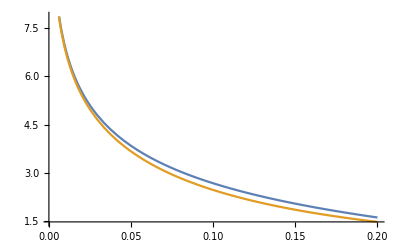

```mathematica
Plot[{tloss2app[10^3,s],tloss2appsimp[10^3,s]},{s,0.001,0.2}]
```

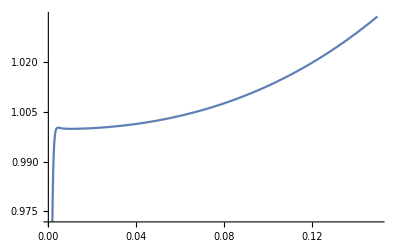

```mathematica
Plot[{tloss2ex[10^3,s]/tloss2app[10^3,s]},{s,0.001,0.15}]
```

```mathematica
Simplify[tloss1app[Nn,s]+tloss2app[Nn,s]]
```

2+3 s+(2 (1+s))/(-1+2 Nn s)-2 (1+s) (EulerGamma+Log[2 s])

```mathematica
2+3 s+(2 (1+s))/(-1+2 Nn s)-2 (1+s) (EulerGamma+Log[2 s])
```

```mathematica
Simplify[tloss1app[Nn,s]+tloss2appsimp[Nn,s]]
```

2-2 EulerGamma+1/(Nn s)+3 s-2 Log[2 s]

#### Approximation for tloss if Ns > 2

Therefore, we obtain our approximations for tloss (accurate if Nn s > 2)

```mathematica
tlossapp[Nn_,s_]:=2(-(1+s) (EulerGamma+Log[2 s])+1+3/2 s+(1+s)/(2 Nn s-1))
```

and the slightly simpler

```mathematica
tlossappsimp[Nn_,s_]:=2(-Log[2 s]+1-EulerGamma+1/(2Nn s))
```

```mathematica
{tlossapp[10^3,0.05],tlossappsimp[10^3,0.05],tlossex[10^3,0.05]}
```

{5.79449,5.47074,5.80568}

#### Very weak selection (s → 0)

```mathematica
FullSimplify[Series [s*tloss1ex[Nn,s],{s,0,4},Assumptions->Nn>1],Assumptions->{s>0,Nn>1}]
```

2 s+1/9 (2-3 Nn) s^3+O[s]^4

```mathematica
FullSimplify[Series [s*tloss2ex[Nn,s],{s,0,4},Assumptions->Nn>1],Assumptions->{s>0,Nn>1}]
```

(-2+(2 Nn Log[Nn])/(-1+Nn)) s+1/9 (-2+Nn-5 Nn^2+(6 Nn^2 Log[Nn])/(-1+Nn)) s^3+O[s]^4

```mathematica
Simplify[2 s+(-2+(2 Nn Log[Nn])/(-1+Nn)) s]
```

(2 Nn s Log[Nn])/(-1+Nn)

```mathematica
FullSimplify[Series [(tloss1ex[Nn,s]+tloss2ex[Nn,s]),{s,0,5},Assumptions->Nn>1],Assumptions->{s>0,Nn>1}]
```

(2 Nn Log[Nn])/(-1+Nn)+O[s]^1

This gives the neutral result of Kimura and Ohta (1969) of 2 Log[N].

#### Approximation for tloss if Ns ≤ 2

We use tlossappsimp[s, Nn] for Nn s  > 2. Then we use tloss[N, 0] ~ 2 Log[Nn] and perform a linear approximation for s < 2/Nn.

```mathematica
FullSimplify[(2 Log[Nn]-tlossappsimp[Nn,2/Nn])/(2/Nn),Assumptions->Nn>0]
```

Nn (-5/4+EulerGamma+Log[4])

```mathematica
tlossappsimp[Nn,2/Nn]/.Nn->10^4.
```

16.9937

```mathematica
tlosssmallsimp[Nn_,s_]:=2 Log[Nn]-s Nn(EulerGamma+Log[4]-5/4)
```

```mathematica
N[-5/4+EulerGamma+Log[4]]
```

0.71351

Here is a slightly more accurate version :

```mathematica
FullSimplify[(2 Log[Nn]-tlossapp[Nn,2/Nn])/(2/Nn),Assumptions->Nn>0]
```

-11/3+EulerGamma (2+Nn)+Nn (-4/3+Log[4])+Log[16]-2 Log[Nn]

```mathematica
tlosssmall[Nn_,s_]:=2 Log[Nn]-s (-11/3+2EulerGamma +Log[16]-2 Log[Nn]+Nn (-4/3+EulerGamma+Log[4]))
```

```mathematica
Simplify[tlosssmallneu[Nn,2/Nn]-tlossapp[Nn,2/Nn],Assumptions->Nn>1]
```

0

#### Plots

```mathematica
linestyleloss1={Directive[AbsoluteThickness[2],Orange],Directive[AbsoluteThickness[2],Red],Directive[AbsoluteThickness[2],Red,Dashed],Directive[AbsoluteThickness[2],Black],Directive[AbsoluteThickness[2],RGBColor[0,0.1,1]]};legendloss1=LineLegend[linestyleloss1,{"t_loss^(small)", "t_loss^(app)", "t_loss^(app)","t_loss^(exact)", "(t̄)_loss"},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->13],LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),LegendMargins->0];
```

```mathematica
linestyleloss2={Directive[AbsoluteThickness[2],RGBColor[0,0.1,1],Dashed],Directive[AbsoluteThickness[2],RGBColor[0,0.1,1]],Directive[AbsoluteThickness[2],Red,Dashed],Directive[AbsoluteThickness[2],Red]};legendloss2=LineLegend[linestyleloss2,{"t_loss, N=10^4", "(t̄)_loss, N=10^4","t_loss, N=10^2","(t̄)_loss, N=10^2"},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->13],LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),LegendMargins->0];
legendloss3=LineLegend[linestyleloss2,{"t_loss, N=10^4", "(t̄)_loss, N=10^4","t_loss, N=10^3","(t̄)_loss, N=10^3"},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->13],LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),LegendMargins->0];
```

```mathematica
tlossapp[10^4,Exp[s]-1]/.s->2/10^4.
```

17.1637

```mathematica
tlosssmall[10^4,Exp[s]-1]/.s->2/10^4.
```

17.1638

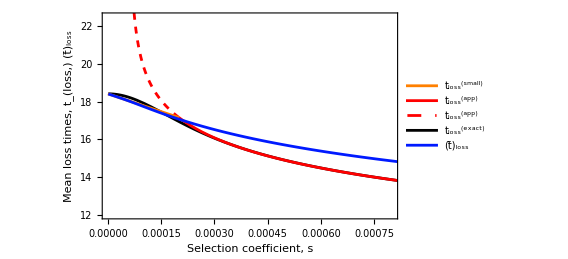

```mathematica
plottloss1a=Plot[tlosssmall[10^4,Exp[s]-1],{s,0,2/10^4},PlotRange->All,PlotStyle->linestyleloss1[[1]],AxesOrigin->{0,0}];
plottloss1b=Plot[tlossapp[10^4,Exp[s]-1],{s,5*10^(-5),2/10^4},PlotRange->All,PlotStyle->linestyleloss1[[3]],AxesOrigin->{0,0}];
plottloss1c=Plot[tlossapp[10^4,Exp[s]-1],{s,2/10^4,0.001},PlotStyle->linestyleloss1[[2]],PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{Style["Selection coefficient, s",FontFamily->"Helvetica",FontSize->13,Black],Style["Mean loss times, t_(loss,) (t̄)_loss",FontFamily->"Helvetica",FontSize->13,Black]},
LabelStyle->13,FrameTicksStyle->Directive[Black,13],ImageSize->400];
plottloss1d=Plot[{tlossNInt[10^4,Exp[s]-1]},{s,10^(-6),0.001},PlotStyle->linestyleloss1[[4]],PlotRange->{0,30},Frame->{{True,False},{True,False}},FrameLabel->{Style["Selection coefficient, s",FontFamily->"Helvetica",FontSize->13,Black],Style["Mean loss times, t_(loss,) (t̄)_loss",FontFamily->"Helvetica",FontSize->13,Black]},
LabelStyle->13,FrameTicksStyle->Directive[Black,13],ImageSize->420];
plotbartloss1=Plot[bartlossnumsigma[10^4,Exp[s]-1],{s,10^(-6),0.001},PlotStyle->linestyleloss1[[5]]]; 
Legended[Show[{plottloss1d,plottloss1b,plottloss1c,plottloss1a,plotbartloss1},PlotRange->{{0,0.0008},{12,22.5}}],Placed[legendloss1,{0.84,0.66}]]
```

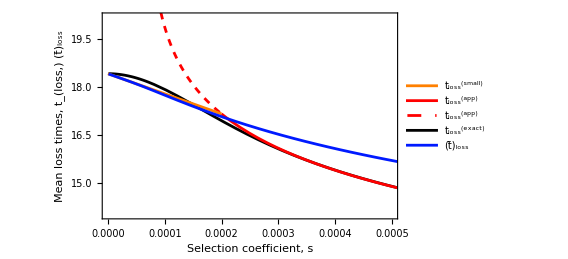

```mathematica
Legended[Show[{plottloss1d,plottloss1b,plottloss1c,plottloss1a,plotbartloss1},PlotRange->{{0.,0.0005},{14.0,20.2}}],Placed[legendloss1,{0.87,0.68}]]
```

## 3.3. Averaging over the (exponential) mutation distribution

### 3.3.1 Compute and plot bartfix by numerical integration

∫_0^∞ tfix[N,e^(s α)]Pfix[N,e^(s α)]Exp[-α]ⅆα / ∫_0^∞ Pfix[N,e^(s α)]Exp[-α]ⅆα

```mathematica
PfixDif[Nn_,s_]:=(1-Exp[-2s])/(1-Exp[-2Nn s]);
```

We use the piecewise function tastHP[Nn, s α] + tfixsmall[Nn, s α].

Here is the critical value of α, at which are concatenated.

```mathematica
αcritHP[Nn_,s_]:=3/(2 Nn s)
```

Selection coefficient if selection acts on the trait:

```mathematica
stilde[s_, α_] := Exp[s α] - 1;
```

```mathematica
FullSimplify[Integrate[PfixDif[Nn,s α] Exp[-α],{α,0,Infinity},Assumptions->s>0&&Nn>0]]
```

(PolyGamma[0,(2+1/s)/(2 Nn)]-PolyGamma[0,1/(2 Nn s)])/(2 Nn s)

```mathematica
Simplify[Series[(PolyGamma[0,(2+1/s)/(2 Nn)]-PolyGamma[0,1/(2 Nn s)])/(2 Nn s),{Nn,Infinity,1}]]
```

(2 s)/(1+2 s)+O[1/Nn]^2

We define two versions, the first for mutations of effect s α, the second for mutations of effect stilde[s, α].

```mathematica
Clear[bartfixnum,bartfixnumsigma]
```

```mathematica
bartfixnum[Nn_,s_]:=bartfixnum[Nn,s]=(2 Nn s (NIntegrate[tfixHPh[Nn,s α] PfixDif[Nn,s α] Exp[-α],{α,αcritHP[Nn,s],∞}]+NIntegrate[tfixsmall[Nn,s α] PfixDif[Nn,s α] Exp[-α],{α,0,αcritHP[Nn,s]}]))/(PolyGamma[0,(2+1/s)/(2 Nn)]-PolyGamma[0,1/(2 Nn s)]);
bartfixnumsigma[Nn_,s_]:=bartfixnumsigma[Nn,s]=(NIntegrate[tfixHPh[Nn,stilde[s,α]] PfixDif[Nn,stilde[s,α]] Exp[-α],{α,αcritHP[Nn,s],∞}]+NIntegrate[tfixsmall[Nn,stilde[s,α]] PfixDif[Nn,stilde[s,α]] Exp[-α],{α,0,αcritHP[Nn,s]}])/(NIntegrate[PfixDif[Nn,stilde[s,α]] Exp[-α],{α,0,∞}])
```

```mathematica
linestyle2={Directive[AbsoluteThickness[2],Blue,Dashed],Directive[AbsoluteThickness[2],Blue],Directive[AbsoluteThickness[2],Red,Dashed],Directive[AbsoluteThickness[2],Red]};legend2=LineLegend[linestyle2,{"t_fix^(app), N=10^4", "(t̄)_fix,   N=10^4","t_fix^(app), N=10^3","(t̄)_fix ,   N=10^3"},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->13],LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray]&),LegendMargins->0];
```

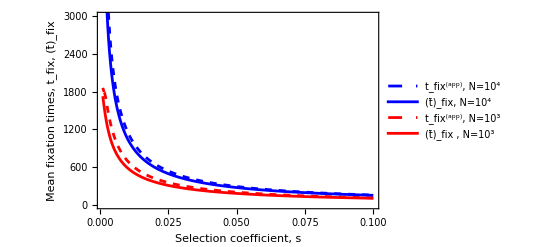

```mathematica
plottfix2a=Plot[tfixapp[10^4,(Exp[s]-1) ],{s,0.001,0.1},PlotStyle->linestyle2[[1]],PlotRange->{0,2*10^4},Frame->{{True,False},{True,False}},FrameLabel->{Style["Selection coefficient, s",FontFamily->"Helvetica",FontSize->13,Black],Style["Mean fixation times, t_fix, (t̄)_fix",FontFamily->"Helvetica",FontSize->13,Black]},
LabelStyle->13,FrameTicksStyle->Directive[Black,13],ImageSize->400];
plottfix2b=Plot[tfixapp[10^3,(Exp[s]-1) ],{s,0.001,0.1},PlotStyle->linestyle2[[3]],PlotRange->{0,2*10^4},Frame->{{True,False},{True,False}},FrameLabel->{Style["Selection coefficient, s",FontFamily->"Helvetica",FontSize->13,Black],Style["Mean fixation times, t_fix, (t̄)_fix",FontFamily->"Helvetica",FontSize->13,Black]},
LabelStyle->13,FrameTicksStyle->Directive[Black,13],ImageSize->400];
plotbartfix2a=Plot[bartfixnumsigma[10^4,s],{s,0.001,0.1},PlotStyle->linestyle2[[2]],PlotRange->All];
plotbartfix2b=Plot[bartfixnumsigma[10^3,s],{s,0.001,0.1},PlotStyle->linestyle2[[4]],PlotRange->All];
Legended[Show[{plottfix2a,plottfix2b,plotbartfix2a,plotbartfix2b},PlotRange->{0,3000}],Placed[legend2,{0.80,0.72}]]
```

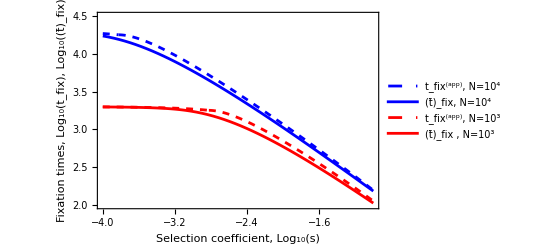

```mathematica
plottfix2alog=Plot[Log[10,tfixapp[10^4,(Exp[10^s]-1) ]],{s,-4,-1},PlotStyle->linestyle2[[1]],PlotRange->{0,2*10^4},Frame->{{True,False},{True,False}},FrameLabel->{Style["Selection coefficient, Log_10(s)",FontFamily->"Helvetica",FontSize->13,Black],Style["Fixation times,  Log_10(t_fix), Log_10((t̄)_fix)",FontFamily->"Helvetica",FontSize->13,Black]},
LabelStyle->13,FrameTicksStyle->Directive[Black,13],ImageSize->400];
plottfix2blog=Plot[Log[10,tfixapp[10^3,(Exp[10^s ]-1) ]],{s,-4,-1},PlotStyle->linestyle2[[3]],PlotRange->{0,2*10^4},Frame->{{True,False},{True,False}},FrameLabel->{Style["Selection coefficient, Log_10(s)",FontFamily->"Helvetica",FontSize->13,Black],Style["Log_10(t_fix), Log_10((t̄)_fix)",FontFamily->"Helvetica",FontSize->13,Black]},
LabelStyle->13,FrameTicksStyle->Directive[Black,13],ImageSize->400];
plotbartfix2alog=Plot[Log[10,bartfixnumsigma[10^4,10^s]],{s,-4,-1},PlotStyle->linestyle2[[2]],PlotRange->All];
plotbartfix2blog=Plot[Log[10,bartfixnumsigma[10^3,10^s]],{s,-4,-1},PlotStyle->linestyle2[[4]],PlotRange->All];
Legended[Show[{plottfix2alog,plottfix2blog,plotbartfix2alog,plotbartfix2blog},PlotRange->{{-4,-1},{2,4.5}}],Placed[legend2,{0.80,0.72}]]
```

### 3.3.2 Compute and plot bartloss by numerical integration

```mathematica
FullSimplify[Integrate[(1-PfixDif[Nn,s α]) Exp[-α],{α,0,∞}],Assumptions->Nn>1&&s>0]
```

(-PolyGamma[0,(2+1/s)/(2 Nn)]+PolyGamma[0,1+1/(2 Nn s)])/(2 Nn s)

We proceed analogously and define

```mathematica
Clear[bartlossnum,bartlossnumsigma]
```

```mathematica
bartlossnum[Nn_,s_]:=bartlossnum[Nn,s]=(2 Nn s (NIntegrate[tlossapp[Nn,s α] (1-PfixDif[Nn,s α] )Exp[-α],{α,2/(Nn s),∞}]+NIntegrate[tlosssmall[Nn,s α] (1-PfixDif[Nn,s α]) Exp[-α],{α,0,2/(Nn s)}]))/(PolyGamma[0,1+1/(2 Nn s)]-PolyGamma[0,(2+1/s)/(2 Nn)]);
bartlossnumsigma[Nn_,s_]:=bartlossnumsigma[Nn,s]=(NIntegrate[tlossapp[Nn,stilde[s,α]] (1-PfixDif[Nn,stilde[s,α]]) Exp[-α],{α,2/(Nn s),∞}]+NIntegrate[tlosssmall[Nn,stilde[s,α]] (1-PfixDif[Nn,stilde[s,α]]) Exp[-α],{α,0,2/(Nn s)}])/(NIntegrate[(1-PfixDif[Nn,stilde[s,α]]) Exp[-α],{α,0,∞}])
```

```mathematica
bartlossnum[10^4,0.01]
```

9.973

```mathematica
bartlossnumsigma[10^4,0.01]
```

9.96426

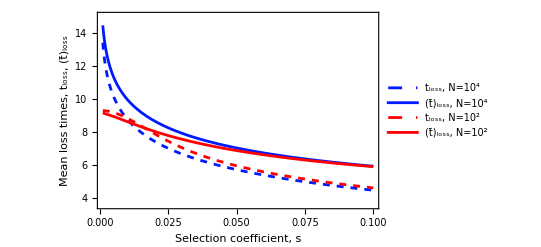

```mathematica
plottloss2a=Plot[tlossapp[10^4,Exp[s]-1],{s,0.001,0.1},PlotStyle->linestyleloss2[[1]],PlotRange->{0,20},Frame->{{True,False},{True,False}},FrameLabel->{Style["Selection coefficient, s",FontFamily->"Helvetica",FontSize->13,Black],Style["Mean loss times, t_loss, (t̄)_loss",FontFamily->"Helvetica",FontSize->13,Black]},
LabelStyle->13,FrameTicksStyle->Directive[Black,13],ImageSize->400];
plottloss2b=Plot[tlossex[10^2,Exp[s]-1],{s,0.001,0.1},PlotStyle->linestyleloss2[[3]],PlotRange->{0,20},Frame->{{True,False},{True,False}},FrameLabel->{Style["Selection coefficient, s",FontFamily->"Helvetica",FontSize->13,Black],Style["Mean loss times, t_loss, (t̄)_loss",FontFamily->"Helvetica",FontSize->13,Black]},
LabelStyle->13,FrameTicksStyle->Directive[Black,13],ImageSize->400];
plotbartloss2a=Plot[bartlossnumsigma[10^4,s],{s,0.001,0.1},PlotStyle->linestyleloss2[[2]],PlotRange->All];
plotbartloss2b=Plot[bartlossnumsigma[10^2,s],{s,0.001,0.1},PlotStyle->linestyleloss2[[4]],PlotRange->All];
Legended[Show[{plottloss2a,plottloss2b,plotbartloss2a,plotbartloss2b},PlotRange->{{0.001,0.1},{3.6,15}},AxesOrigin->{0,4}],Placed[legendloss2,{0.80,0.72}]]
```

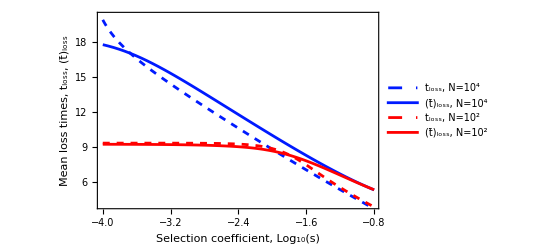

```mathematica
plottloss2alog=Plot[tlossapp[10^4,Exp[10^s]-1],{s,-4,-0.8},PlotStyle->linestyleloss2[[1]],PlotRange->{0,20},Frame->{{True,False},{True,False}},FrameLabel->{Style["Selection coefficient, Log_10(s)",FontFamily->"Helvetica",FontSize->13,Black],Style["Mean loss times, t_loss, (t̄)_loss",FontFamily->"Helvetica",FontSize->13,Black]},
LabelStyle->13,FrameTicksStyle->Directive[Black,13],ImageSize->400];
plottloss2blog=Plot[tlossex[10^2,Exp[10^s]-1],{s,-4,-0.8},PlotStyle->linestyleloss2[[3]],PlotRange->{0,20},Frame->{{True,False},{True,False}},FrameLabel->{Style["Selection coefficient, Log_10(s)",FontFamily->"Helvetica",FontSize->13,Black],Style["Mean loss times, t_loss, (t̄)_loss",FontFamily->"Helvetica",FontSize->13,Black]},
LabelStyle->13,FrameTicksStyle->Directive[Black,13],ImageSize->400];
plotbartloss2alog=Plot[bartlossnumsigma[10^4,10^s],{s,-4,-0.8},PlotStyle->linestyleloss2[[2]],PlotRange->All];
plotbartloss2blog=Plot[bartlossnumsigma[10^2,10^s],{s,-4,-0.8},PlotStyle->linestyleloss2[[4]],PlotRange->All];
Legended[Show[{plottloss2alog,plottloss2blog,plotbartloss2alog,plotbartloss2blog},PlotRange->{{-4,-0.81},{4.0,20.2}}],Placed[legendloss2,{0.80,0.72}]]
```

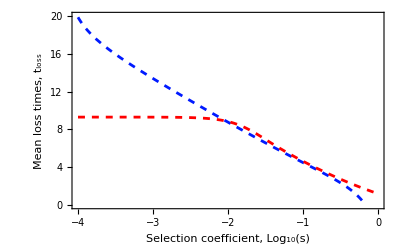

```mathematica
plotloss1=Plot[tlossapp[10^4,Exp[10^s]-1],{s,-4,0},PlotStyle->linestyleloss2[[1]],PlotRange->{0,20},Frame->{{True,False},{True,False}},FrameLabel->{Style["Selection coefficient, Log_10(s)",FontFamily->"Helvetica",FontSize->13,Black],Style["Mean loss times, t_loss",FontFamily->"Helvetica",FontSize->13,Black]},
LabelStyle->13,FrameTicksStyle->Directive[Black,13],ImageSize->400];
plotloss2=Plot[tlossex[10^2,Exp[10^s]-1],{s,-4,0},PlotStyle->linestyleloss2[[3]],PlotRange->{0,20},Frame->{{True,False},{True,False}},FrameLabel->{Style["Selection coefficient, Log_10(s)",FontFamily->"Helvetica",FontSize->13,Black],Style["Mean loss times, t_loss",FontFamily->"Helvetica",FontSize->13,Black]},
LabelStyle->13,FrameTicksStyle->Directive[Black,13],ImageSize->400];
Show[plotloss1,plotloss2]
```

bartloss depends only weakly on N :

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

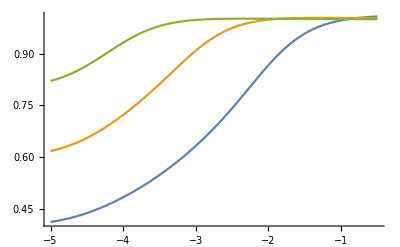

```mathematica
Plot[{bartlossnum[10^2,10^s]/bartlossnum[10^5,10^s],bartlossnum[10^3,10^s]/bartlossnum[10^5,10^s],bartlossnum[10^4,10^s]/bartlossnum[10^5,10^s]},{s,-5,-0.5},PlotRange->All]
```

### 3.3.3 Approximations for bartfix

```mathematica
Simplify[Integrate[PfixDif[Nn,s α]Exp[-α],{α,0,Infinity},Assumptions->Nn>0&&s>0]]
```

(PolyGamma[0,(2+1/s)/(2 Nn)]-PolyGamma[0,1/(2 Nn s)])/(2 Nn s)

```mathematica
Simplify[Series[(PolyGamma[0,(2+1/s)/(2 Nn)]-PolyGamma[0,1/(2 Nn s)])/(2 Nn s),{Nn,Infinity,1},Assumptions->Nn>0&&s>0]]
```

(2 s)/(1+2 s)+O[1/Nn]^2

This is equivalent to using the approximation PfixDif[Nn, s α] = 1 - Exp[-2 s α], which we use henceforth :

```mathematica
Simplify[Integrate[(1-Exp[-2s α])Exp[-α],{α,0,Infinity},Assumptions->Nn>0&&s>0]]
```

(2 s)/(1+2 s)

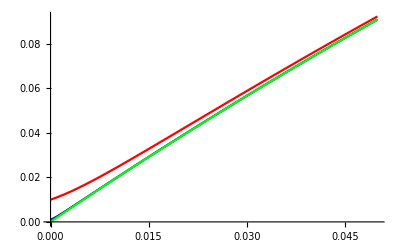

```mathematica
Plot[{(PolyGamma[0,(2+1/s)/(2 Nn)]-PolyGamma[0,1/(2 Nn s)])/(2 Nn s)/.Nn->10^2,(PolyGamma[0,(2+1/s)/(2 Nn)]-PolyGamma[0,1/(2 Nn s)])/(2 Nn s)/.Nn->10^3,(2 s)/(1+2 s)},{s,0,0.05},PlotStyle->{Red,Blue,Green}]
```

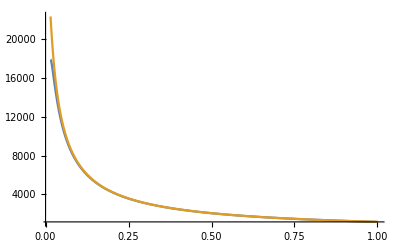

```mathematica
Plot[{tfixHPh[10^4,s α]/.s->0.01,(2 (EulerGamma+Log[2 10^4 s α]))/(s α)/.s->0.01},{α,αcritHP[10^4,0.01],1},PlotRange->All]
```

Instead of tfixHP we use the simplified version 2 (EulerGamma + Log[2 Nn s α])/(s α).

```mathematica
FullSimplify[Integrate[(2 (EulerGamma+Log[2 Nn s α]))/(s α) (1-ⅇ^(-2 s α))Exp[-α],{α,αcritHP[Nn,s],Infinity},Assumptions->Nn>0&&s>0]]
```

1/s 2 ((Gamma[0,3/(2 Nn s)]-Gamma[0,(3+6 s)/(2 Nn s)]) (EulerGamma+Log[3])+MeijerG[{{},{1,1}},{{0,0,0},{}},3/(2 Nn s)]-MeijerG[{{},{1,1}},{{0,0,0},{}},(3+6 s)/(2 Nn s)])

```mathematica
Simplify[Series[%,{Nn,Infinity,1},Assumptions->s>0]]
```

((Log[6]+2 Log[Nn]-Log[3+3/(2 s)]-Log[1/s]) (Log[3+3/(2 s)]-Log[3/(2 s)]))/s-(6 (-1+EulerGamma+Log[3]))/(s Nn)+O[1/Nn]^2

```mathematica
FullSimplify[Normal[%],Assumptions->Nn>1&&s>0]
```

(-6 (-1+EulerGamma+Log[3])+Nn Log[(4 Nn^2 s^2)/(1+2 s)] Log[1+2 s])/(Nn s)

```mathematica
N[-1+EulerGamma+Log[3]]
```

0.675828

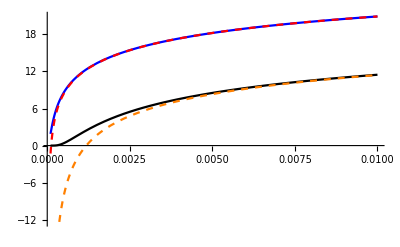

```mathematica
Plot[{1/s 2 ((Gamma[0,3/(2 Nn s)]-Gamma[0,(3+6 s)/(2 Nn s)]) (EulerGamma+Log[3])+MeijerG[{{},{1,1}},{{0,0,0},{}},3/(2 Nn s)]-MeijerG[{{},{1,1}},{{0,0,0},{}},(3+6 s)/(2 Nn s)])/.Nn->10^4,(-6 (-1+EulerGamma+Log[3])+Nn Log[(4 Nn^2 s^2)/(1+2 s)] Log[1+2 s])/(Nn s)/.Nn->10^4,1/s 2 ((Gamma[0,3/(2 Nn s)]-Gamma[0,(3+6 s)/(2 Nn s)]) (EulerGamma+Log[3])+MeijerG[{{},{1,1}},{{0,0,0},{}},3/(2 Nn s)]-MeijerG[{{},{1,1}},{{0,0,0},{}},(3+6 s)/(2 Nn s)])/.Nn->10^3,(-6 (-1+EulerGamma+Log[3])+Nn Log[(4 Nn^2 s^2)/(1+2 s)] Log[1+2 s])/(Nn s)/.Nn->10^3},{s,10^(-4),0.01},PlotStyle->{Blue,Directive[Red,Dashed],Black,Directive[Orange,Dashed]}]
```

```mathematica
Simplify[Series[Log[1+2s],{s,0,2}]]
```

2 s-2 s^2+O[s]^3

```mathematica
bartfixapp1[Nn_,s_]:=(Nn  Log[1+2 s](2Log[2Nn s]-Log[1+2s])-6 (-1+EulerGamma+Log[3]))/(Nn s)
```

```mathematica
Simplify[Integrate[(2(Log[2 Nn s α]+EulerGamma))/(s α) (1-ⅇ^(-2 s α))Exp[-α],{α,0,Infinity},Assumptions->Nn>0&&s>0&&a>0]]
```

((2 Log[2 Nn s]-Log[1+2 s]) Log[1+2 s])/s

```mathematica
FullSimplify[Integrate[tfixsmall[Nn,s α](1-ⅇ^(-2 s α))Exp[-α],{α,0,αcritHP[Nn,s]},Assumptions->Nn>0&&s>0]]
```

1/(27 (1+2 s)^2)2 ⅇ^(-(3+6 s)/(2 Nn s)) Nn (2 (-3+9 EulerGamma+6 EulerGamma (3+Nn) s+9 Log[3]+s (-6-11 Nn+6 (3+Nn) Log[3]))-2 ⅇ^(3/Nn) (1+2 s)^2 (-3+EulerGamma (9+6 Nn s)+9 Log[3]+Nn s (-11+Log[729]))+2 ⅇ^((3+6 s)/(2 Nn s)) s (27+54 s+4 Nn s (1+s) (-11+6 EulerGamma+Log[729])))

```mathematica
Simplify[Normal[Series[%,{Nn,Infinity,1}]],Assumptions->Nn>1&&s>0]
```

(5+12 EulerGamma+Log[531441])/(6 Nn s)

```mathematica
FactorInteger[531441]
```

{{3,12}}

```mathematica
bartfixapp2[Nn_,s_]:=(2 EulerGamma+2Log[3]+5/6)/(Nn s)
```

```mathematica
N[2 EulerGamma+2Log[3]+5/6]
```

4.18499

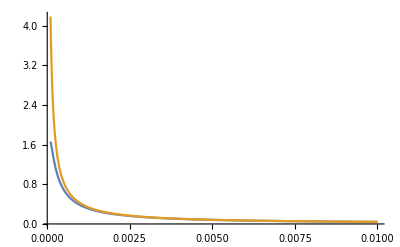

```mathematica
Plot[{1/(27 (1+2 s)^2)2 ⅇ^(-(3+6 s)/(2 Nn s)) Nn (2 (-3+9 EulerGamma+6 EulerGamma (3+Nn) s+9 Log[3]+s (-6-11 Nn+6 (3+Nn) Log[3]))-2 ⅇ^(3/Nn) (1+2 s)^2 (-3+EulerGamma (9+6 Nn s)+9 Log[3]+Nn s (-11+Log[729]))+2 ⅇ^((3+6 s)/(2 Nn s)) s (27+54 s+4 Nn s (1+s) (-11+6 EulerGamma+Log[729])))/.Nn->10^4,bartfixapp2[10^4,s]},{s,10^(-4),0.01},PlotRange->All]
```

Here is our approximation for bartfix.

```mathematica
bartfixapp[Nn_,s_]:=((1+2s)(bartfixapp1[Nn,s]+bartfixapp2[Nn,s]))/(2s)
```

```mathematica
FullSimplify[bartfixapp[Nn,s]]
```

((1+2 s) (41-24 EulerGamma-24 Log[3]+6 Nn (2 Log[2 Nn s]-Log[1+2 s]) Log[1+2 s]))/(12 Nn s^2)

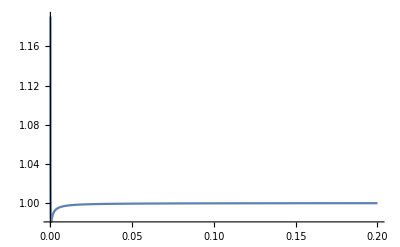

```mathematica
Plot[{bartfixnum[10^4,s]/bartfixapp[10^4,s]},{s,10^(-4),0.2},PlotRange->All]
```

We can rewrite bartfixapp as

```mathematica
((1+2 s) (41/6-4 EulerGamma-4 Log[3]))/(2s^2Nn)+((1+2s) Log[1+2 s](2 Log[2 Nn s]-Log[1+2 s]))/(2s^2)
```

```mathematica
FullSimplify[((1+2 s) (41/6-4 EulerGamma-4 Log[3]))/(2s^2Nn)+((1+2s) Log[1+2 s](2 Log[2 Nn s]-Log[1+2 s]))/(2s^2)-bartfixapp[Nn,s]]
```

0

Because

```mathematica
N[(41/6-4 EulerGamma-4 Log[3])]
```

0.130022

the term (1 + 2 s) (41/6 - 4 EulerGamma - 4 Log[3]) /(2 s^2 Nn) can be neglected.

Therefore, we arrive at the simple approximation:

```mathematica
bartfixapps[Nn_,s_]:=((1+2s) Log[1+2 s](2 Log[2 Nn s]-Log[1+2 s]))/(2s^2)
```

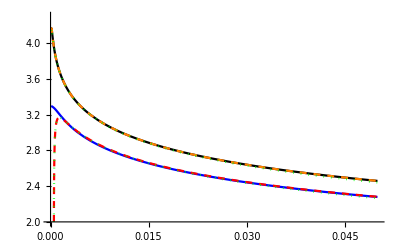

```mathematica
Plot[{Log[10,bartfixnum[10^3,s]],Log[10,bartfixapps[10^3,s]],Log[10,bartfixapps[10^4,s]],Log[10,bartfixapps[10^4,s]],Log[10,(2Log[2*10^4 s])/s],Log[10,(2Log[2*10^3s])/s]},{s,10^(-4),0.05},PlotRange->{2,4.3},PlotStyle->{Blue,Directive[Red,Dashed],Black,Directive[Orange,Dashed],Directive[Green,Dotted],Directive[Green,Dotted]}]
```

bartfixapps can be further simplified (see green dotted curves above):

```mathematica
bartfixappsimp[Nn_,s_]:=(2Log[2Nn s])/s
```

For general αbar, we substitute s  → s αbar.

### 3.3.4 Approximations for bartloss

```mathematica
Simplify[Integrate[(1-PfixDif[Nn,s α])Exp[-α],{α,0,Infinity},Assumptions->Nn>0&&s>0]]
```

(-PolyGamma[0,(2+1/s)/(2 Nn)]+PolyGamma[0,1+1/(2 Nn s)])/(2 Nn s)

```mathematica
Simplify[Series[(-PolyGamma[0,(2+1/s)/(2 Nn)]+PolyGamma[0,1+1/(2 Nn s)])/(2 Nn s),{Nn,Infinity,1},Assumptions->Nn>0&&s>0]]
```

1/(1+2 s)+O[1/Nn]^2

This is equivalent to using the approximation PfixDif[Nn, s α] = 1 - Exp[-2 s α], which we use henceforth :

```mathematica
Simplify[Integrate[Exp[-2s α]Exp[-α],{α,0,Infinity},Assumptions->Nn>0&&s>0]]
```

1/(1+2 s)

We use the simple approximations tlossappsimp and tlosssmallsimp.

```mathematica
FullSimplify[Integrate[(1+2s)tlossappsimp[Nn,s α] ⅇ^(-2 s α)Exp[-α],{α,2/(Nn s),Infinity},Assumptions->Nn>0&&s>0]]
```

((-1+2 (-1+Nn) s) ExpIntegralEi[-(2+4 s)/(Nn s)])/(Nn s)-2 ⅇ^(-(2+4 s)/(Nn s)) (-1+EulerGamma+Log[4]-Log[Nn])

This can be simplified by using Nn ≈  Nn - 1 and

```mathematica
Simplify[Series[ExpIntegralEi[-x],{x,0,1}],Assumptions->x>0]
```

(EulerGamma+Log[x])-x+O[x]^2

We obtain

```mathematica
Simplify[((-1+2 Nn s) (-(2+4 s)/(Nn s)+EulerGamma+Log[2+4s]-Log[Nn s]))/(Nn s)-2 ⅇ^(-(2+4 s)/(Nn s)) (-1+EulerGamma+Log[4]-Log[Nn])]
```

-2 ⅇ^(-(2+4 s)/(Nn s)) (-1+EulerGamma+Log[4]-Log[Nn])+((-1+2 Nn s) (-2-4 s+EulerGamma Nn s-Nn s Log[Nn s]+Nn s Log[2+4 s]))/(Nn^2 s^2)

```mathematica
Simplify[Integrate[(1+2s)tlosssmallsimp[Nn,s α] ⅇ^(-2 s α)Exp[-α],{α,0,2/(Nn s)},Assumptions->Nn>0&&s>0]]
```

(ⅇ^(-(2+4 s)/(Nn s)) (-((-2+(-4+(-1+ⅇ^((2+4 s)/(Nn s))) Nn) s) (-5+4 EulerGamma+Log[256]))+8 (-1+ⅇ^((2+4 s)/(Nn s))) (1+2 s) Log[Nn]))/(4 (1+2 s))

The first term, -((-2 + (-4 + (-1 + Exp[(2 + 4 s)/(Nn s)]) Nn) s) (-5 + 4 EulerGamma + Log[256])), can be neglected:

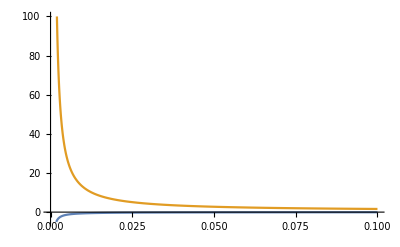

```mathematica
Plot[{-((-2+(-4+(-1+ⅇ^((2+4 s)/(Nn s))) Nn) s) (-5+4 EulerGamma+Log[256]))/.Nn->10^3,8 (-1+ⅇ^((2+4 s)/(Nn s))) (1+2 s) Log[Nn]/.Nn->10^3},{s,10^(-4),0.1},PlotRange->{-5,100}]
```

Therefore, we obtain

```mathematica
Simplify[(ⅇ^(-(2+4 s)/(Nn s)) (0+8 (-1+ⅇ^((2+4 s)/(Nn s))) (1+2 s) Log[Nn]))/(4 (1+2 s))]
```

2 (1-ⅇ^(-(2+4 s)/(Nn s))) Log[Nn]

Summing up the two approximations yields

```mathematica
FullSimplify[-2 ⅇ^(-(2+4 s)/(Nn s)) (-1+EulerGamma+Log[4]-Log[Nn])+((-1+2 Nn s) (-2-4 s+EulerGamma Nn s-Nn s Log[Nn s]+Nn s Log[2+4 s]))/(Nn^2 s^2)+2 (1-ⅇ^(-(2+4 s)/(Nn s))) Log[Nn]]
```

-2 ⅇ^(-(2+4 s)/(Nn s)) (-1+EulerGamma+Log[4])+2 Log[Nn]+((-1+2 Nn s) (-2+(-4+EulerGamma Nn) s+Nn s (-Log[Nn s]+Log[2+4 s])))/(Nn^2 s^2)

Using Log[2+4s] ≈ 2+2s, yields

the following approximation for bartloss:

```mathematica
bartlossappx[Nn_,s_]:=2 Log[Nn]-2 ⅇ^(-(2+4 s)/(Nn s)) (EulerGamma+2Log[2]-1)+(2-1/(Nn s))(-Log[Nn s]+Log[2]+EulerGamma+2s-(2+4s)/(Nn s));
```

However, the term 2 Log[Nn] is misleading because it cancels :

```mathematica
FullSimplify[-2Log[s]+2(Log[2]+EulerGamma+2s)-2 ⅇ^(-(2+4 s)/(Nn s)) (EulerGamma+2Log[2]-1)+1/(Nn s)(Log[Nn s]-Log[2]-EulerGamma-(2+4s)(2-1/(Nn s))-2s)-bartlossappx[Nn,s],Assumptions->Nn>1&&s>0]
```

0

Therefore, we rewrite bartlossappx as

```mathematica
bartlossapp[Nn_,s_]:=-2Log[s]+2(Log[2]+EulerGamma+2s)-2 ⅇ^(-(2+4 s)/(Nn s)) (EulerGamma+2Log[2]-1)+1/(Nn s)(Log[Nn s]-Log[2]-EulerGamma-(2+4s)(2-1/(Nn s))-2s)
```

```mathematica
FullSimplify[bartlossappx[Nn,s]-bartlossapp[Nn,s],Assumptions->Nn>1&&s>0]
```

0

A simpler approximation is obtained as follows:

```mathematica
FullSimplify[Normal[Series[bartlossapp[Nns/s,s],{Nns,Infinity,1}]]/.Nns->Nn s,Assumptions->Nn>1&&s>0]
```

2+4 s+Log[1/(4 s^2)]+(-8+EulerGamma (3+8 s)+2 s (-9+Log[256])+Log[128 Nn s])/(Nn s)

```mathematica
Simplify[N[-8+EulerGamma (3+8 s)+2 s (-9+Log[256])+Log[128]+Log[ Nn s]]]
```

-1.41632-2.29192 s+1. Log[Nn s]

```mathematica
N[-8+3EulerGamma+7Log[2]]
```

-1.41632

```mathematica
Simplify[2+4 s+Log[1/(4 s^2)]-2(-Log[2s]+1+2s),Assumptions->s>0]
```

0

This yields the following very simple approximation for bartloss:

```mathematica
bartlossappsimp[Nn_,s_]:=2(-Log[2s]+1+2s)-(1.42-Log[Nn s])/(Nn s)
```

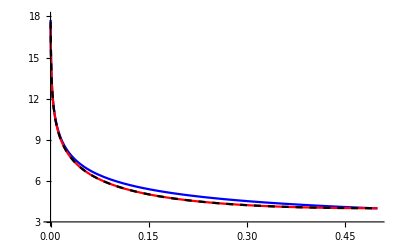

```mathematica
Plot[{bartlossnum[10^4,s],bartlossapp[10^4,s],bartlossappsimp[10^4,s]},{s,10^(-4),0.5},PlotRange->{3,18},PlotStyle->{Blue,Red,Directive[Black,Dashed]}]
```

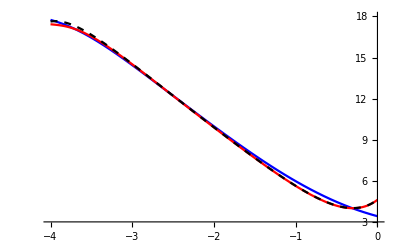

```mathematica
Plot[{bartlossnum[10^4,10^s],bartlossapp[10^4,10^s],bartlossappsimp[10^4,10^s]},{s,-4,0},PlotRange->{3,18},PlotStyle->{Blue,Red,Directive[Black,Dashed],Orange}]
```

The proxy works also for stilde if s < 10^(-0.5) ≈ 0.32:

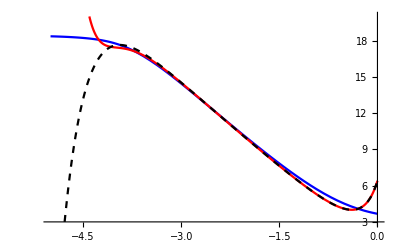

```mathematica
Plot[{bartlossnumsigma[10^4,10^s],bartlossapp[10^4,Exp[10^s]-1],bartlossappsimp[10^4,Exp[10^s]-1]},{s,-5,0},PlotRange->{3,20},PlotStyle->{Blue,Red,Directive[Black,Dashed]}]
```

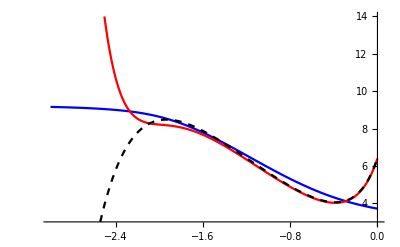

```mathematica
Plot[{bartlossnumsigma[10^2,10^s],bartlossapp[10^2,Exp[10^s]-1],bartlossappsimp[10^2,Exp[10^s]-1]},{s,-3,0},PlotRange->{3,14},PlotStyle->{Blue,Red,Directive[Black,Dashed]}]
```

Clearly, both proxies require Nn s > 1.